```mathematica
Quit
```

The notebook illustrates how to use the package AnalyticSpinOrbitsHamiltonJacobi , which provides the analytic spin corrections to bound plunging orbits.  See arXiv:2603.04682  (https://arxiv.org/abs/2603.04682 )

PREREQUISITEs: the following packages are neededS
- KerrGeodesics from the BPToolkit. This package is needed to calculate the location of the geodesic separatrix.

If you make use of this notebook, please acknowledge 
- “Piovano”  (https://arxiv.org/abs/2603.04682 )
- KerrGeodesics package,  (https://zenodo.org/records/8108265 ) of the  BHPToolkit

### Convention for EoM

Here we follow the same convention of  CQG, Volume 37, Number 14  (https://iopscience.iop.org/article/10.1088/1361-6382/ab79d5 )

r_1== p/(1-e)
r_2== p/(1+e)
z_1==√(1-x^2)

or

p==2(r_1 r_2)/(r_1+r_2)
e== (r_1-r_2)/(r_1+r_2)
x ==  Sign[ℒ]√(1-z_1^2)

(circular) 0<e<1 (parabolic)
(retrograde) -1 < x < 1 (prograde)
p> p_LSO(e,x)

Equatorial orbits

x==±1
z_1==0
𝒬 ==0

“spar” and “sort” are the parallel and orthogonal component of the spin to the total angular momentum.

### Loading all the necessary files

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<KerrGeodesics`
```

```mathematica
Get["AnalyticSpinOrbitsHamiltonJacobi.wl"]
```

## Generic plunge

IMPORTANT NOTE:The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlunge=0.9`55;
eccPlunge=0.7`55;
```

```mathematica
pPlunge=2.37`55;
```

### Calculation orbits

```mathematica
AbsoluteTiming[corrPlunge=KerrNearEqSpinOrbitCorrFEPlunge[aPlunge,pPlunge,eccPlunge,1];]
```

{0.001032,Null}

### Constants of motion and frequencies

```mathematica
{corrPlunge["Eg"],corrPlunge["Lzg"]}
```

{0.901597676872068988041179515485612777095671898004583737,2.0945034158041101258681121290768577753935773120458114}

BL azimuthal frequency  Ω_ϕ

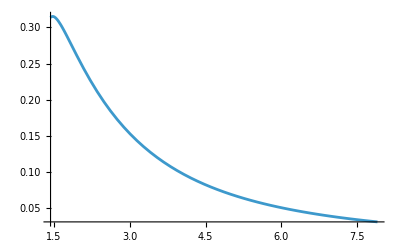

```mathematica
Plot[corrPlunge["BLFrequenciesGeo"][r],{r,1+√(1-aPlunge^2),pPlunge/(1-eccPlunge)}]
```

BL spin precession frequency Ω_p

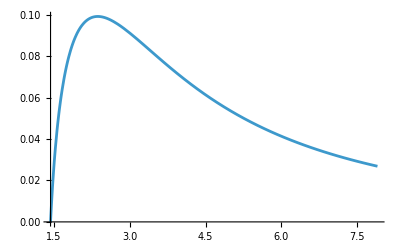

```mathematica
Plot[corrPlunge["BLPrecessionFrequency"][r],{r,1+√(1-aPlunge^2),pPlunge/(1-eccPlunge)}]
```

### Shifts constants of motion

```mathematica
{corrPlunge["Es"],corrPlunge["Jzs"]}
```

{-0.185622923693362571643737861364912206581508580101687,-1.3593162912743629189689803174529137892078848340981}

### Shift frequency

Spin correction to the BL frequencies

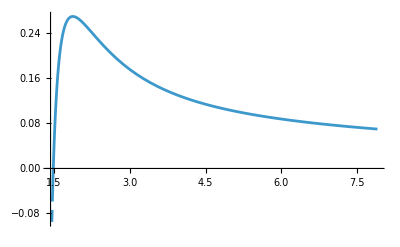

```mathematica
Plot[corrPlunge["BLFrequenciesCorrection"][r],{r,1+√(1-aPlunge^2),pPlunge/(1-eccPlunge)}]
```

### Geodesic coordinate time and azimuthal trajectories

The coordinate time and azimuthal trajectories diverge logarithmically at  diverge at the outer (inner) horizons r_+ (r_-).

```mathematica
{corrPlunge[ "trg"][pPlunge/(1-eccPlunge)],corrPlunge[ "ϕrg"][pPlunge/(1-eccPlunge)]}
```

{0.,0.}

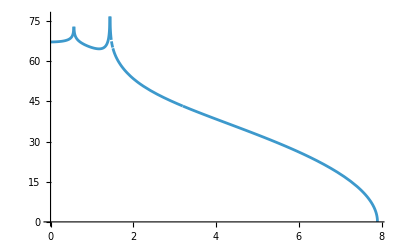

```mathematica
Plot[corrPlunge[ "trg"][r],{r,0,pPlunge/(1-eccPlunge)}]
```

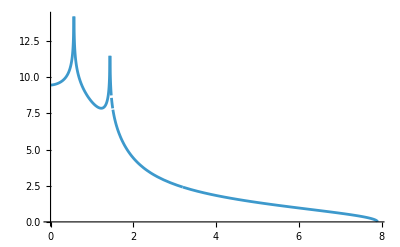

```mathematica
Plot[corrPlunge[ "ϕrg"][r],{r,0,pPlunge/(1-eccPlunge)}]
```

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

Note: the correction to the radial motion, δr(r_g),  diverge as at r_g=0.

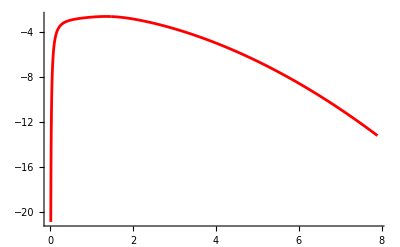

```mathematica
Plot[corrPlunge["δrpar"][r],{r,1/100,pPlunge/(1-eccPlunge)},PlotStyle->Red]
```

#### Spin corrections to the radial velocity

Note: the shift to the radial velocity, dδr/dλ,  diverge as a pole at r_g=0.

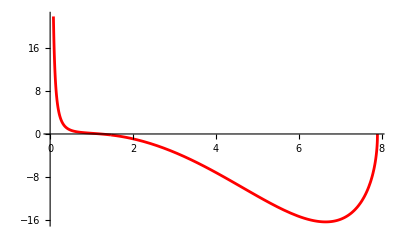

```mathematica
Plot[corrPlunge["δvrpar"][r],{r,1/100,pPlunge/(1-eccPlunge)},PlotStyle->Red]
```

#### Spin corrections to the coordinate time and azimuthal trajectories

The shifts to the coordinate time and azimuthal trajectories diverge as poles at the outer (inner) horizons r_+ (r_-), and at r_g=0.

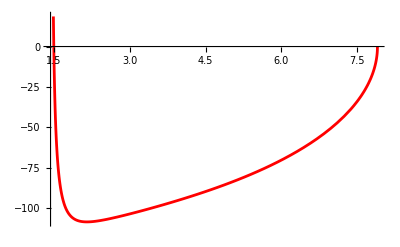

```mathematica
Plot[corrPlunge["δtpar"][r],{r,1+√(1-aPlunge^2),pPlunge/(1-eccPlunge)},PlotStyle->Red]
```

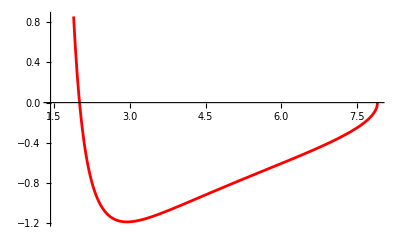

```mathematica
Plot[corrPlunge["δϕpar"][r],{r,1+√(1-aPlunge^2),pPlunge/(1-eccPlunge)},PlotStyle->Red]
```

#### Spin corrections to the coordinate time and azimuthal velocities

Note: the shift to the coordinate time, dδt/dλ, and azimuthal velocities,dδϕ/dλ  diverge as poles at the outer (inner) horizons r_+ (r_-), and at r_g=0.

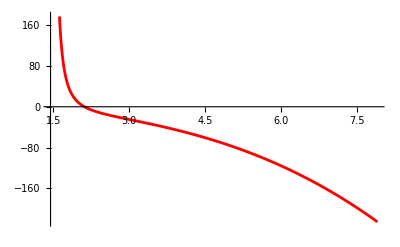

```mathematica
Plot[corrPlunge["δvtpar"][r],{r,1+√(1-aPlunge^2)+1/100,pPlunge/(1-eccPlunge)},PlotStyle->Red]
```

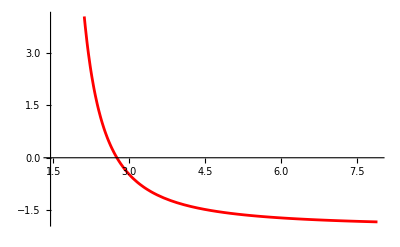

```mathematica
Plot[corrPlunge["δvϕpar"][r],{r,1+√(1-aPlunge^2)+1/100,pPlunge/(1-eccPlunge)},PlotStyle->Red]
```

### Spin corrections orthogonal component of the spin

Precession phase.

```mathematica
{corrPlunge["ψp"][0],corrPlunge["ψp"][pPlunge/(1-eccPlunge)]}
```

{4.649909321392968759415,0.}

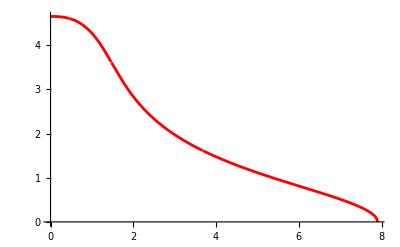

```mathematica
Plot[corrPlunge["ψp"][r],{r,0,pPlunge/(1-eccPlunge)},PlotStyle->Red]
```

Spin correction to the polar motion.  It diverges at r_g=0.

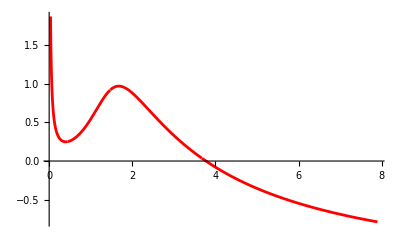

```mathematica
Plot[corrPlunge["δzort"][r],{r,1/30,pPlunge/(1-eccPlunge)},PlotStyle->Red,PlotRange->All]
```

## Generic plunge approaching homoclinic motion

IMPORTANT NOTE:The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlunge=0.9`85;
eccPlunge=0.7`85;
```

```mathematica
pCritical=KerrGeoSeparatrix[aPlunge,eccPlunge,1];
```

We check here that generic plunging orbits reduce to homoclinic orbits in the limit ρ_ig->0.

### Calculation orbits

Generic plunge

```mathematica
AbsoluteTiming[corrNearHom=KerrNearEqSpinOrbitCorrFEPlunge[aPlunge,pCritical-10^(-10),eccPlunge,1];]
```

{0.001205,Null}

Homoclinic orbit

```mathematica
AbsoluteTiming[corrHom=KerrNearEqSpinOrbitCorrFEHom[aPlunge,pCritical,eccPlunge,1];]
```

{0.008512,Null}

### Constants of motion and frequencies

```mathematica
{corrNearHom["Eg"],corrNearHom["Lzg"]}
```

{0.9251648230267833677879095439178093062690496359779440018822838977403345610780922688,2.389367424495292682515464408302741131294231392033062805695347686640446370406692366}

```mathematica
{corrHom["Eg"],corrHom["Lzg"]}
```

{0.925164823029312817049445672840732914428723704532106547630787129360317581586312115,2.3893674245338790585209185530015990389725948046546683963483679493845448359894285}

BL azimuthal frequency  Ω_ϕ

```mathematica
corrNearHom["BLFrequenciesGeo"][pCritical/(1+eccPlunge)]
```

0.299711165994151032248347110975430546565667751437415819635727788257230052467025562

```mathematica
corrHom["BLFrequenciesGeo"][[3]]
```

0.29971116599692448611637275244725118919898074647717837925053608289280949520541887

```mathematica
corrNearHom["BLPrecessionFrequency"][pCritical/(1+eccPlunge)]
```

0.0857955288262232342998328731304936831030021060254068638978220922030630802684668501

```mathematica
corrHom["BLPrecessionFrequency"]
```

0.08579552882688666323621197436760379092008389801522206793536885091623969017292775

### Shifts constants of motion

```mathematica
{corrNearHom["Es"],corrNearHom["Jzs"]}
```

{-0.03191977617525035165926640268378068542864941756913937658369317301649182409645505,0.1797589103990824803287337628989589984124204036296023288966484982446751540067438}

```mathematica
{corrHom["Es"],corrHom["Jzs"]}
```

{-0.031919776169274367081759710310956439466756012472750696647951109798226816058397,0.17975891047771355698950562155548060585321120490006778807408074686277357210332}

### Shifts frequency

Spin correction BL azimuthal frequency Ω_ϕ

```mathematica
corrNearHom["BLFrequenciesCorrection"][pCritical/(1+eccPlunge)]
```

0.0643825813830369341848422063551308273729169555591831830438732845382795

```mathematica
corrHom["BLFrequenciesCorrection"]
```

{0.0643831071456275752940031538905033173994421230761367574665686677436490720095}

### Geodesic trajectories

Geodesic radial velocity

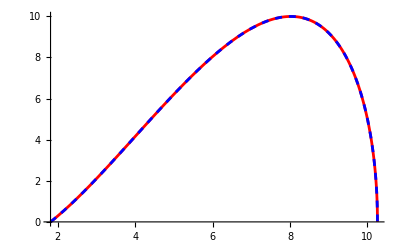

```mathematica
Show[Plot[corrHom["vrg"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->Red],Plot[corrNearHom["vrg"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->{Blue,Dashed}]]
```

The coordinate time and azimuthal trajectories diverge logarithmically at the periastron

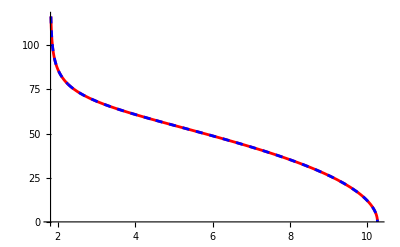

```mathematica
Show[Plot[corrHom["trg"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->Red],Plot[corrNearHom["trg"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->{Blue,Dashed},WorkingPrecision->20]]
```

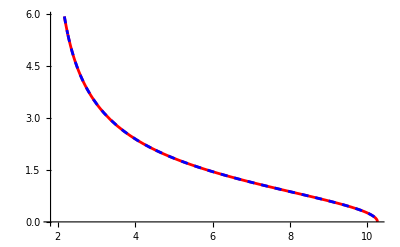

```mathematica
Show[Plot[corrHom["ϕrg"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->Red],Plot[corrNearHom["ϕrg"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->{Blue,Dashed},WorkingPrecision->20]]
```

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

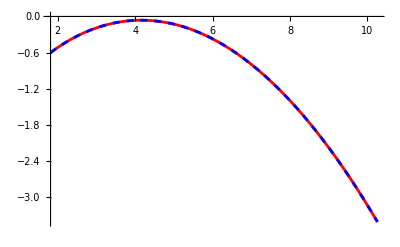

```mathematica
Show[Plot[corrHom["δrpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->Red],Plot[corrNearHom["δrpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->{Blue,Dashed},WorkingPrecision->20]]
```

#### Spin corrections to the radial velocity

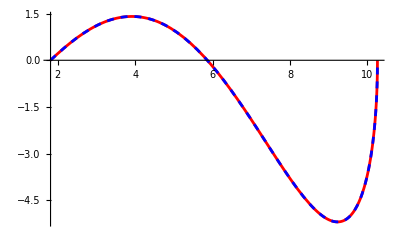

```mathematica
Show[Plot[corrHom["δvrpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->Red],Plot[corrNearHom["δvrpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->{Blue,Dashed},WorkingPrecision->20]]
```

#### Spin corrections to the coordinate time and azimuthal trajectories

Note: the shift to the coordinate time, dδt/dλ, and azimuthal velocities,dδϕ/dλ, are diverging at r_g=r_(2g) like their geodesic counterparts.

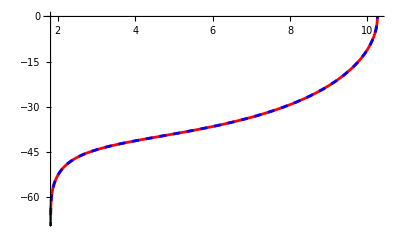

```mathematica
Show[Plot[corrHom["δtpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->Red],Plot[corrNearHom["δtpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->{Blue,Dashed}]]
```

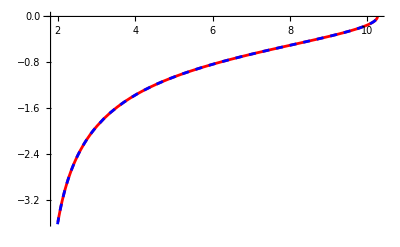

```mathematica
Show[Plot[corrHom["δϕpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->Red],Plot[corrNearHom["δϕpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->{Blue,Dashed}]]
```

#### Spin corrections to the coordinate time and azimuthal velocities

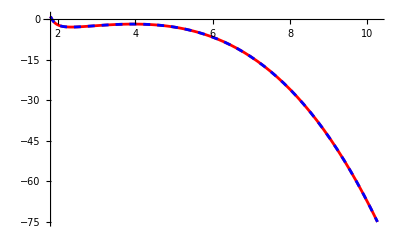

```mathematica
Show[Plot[corrHom["δvtpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->Red],Plot[corrNearHom["δvtpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->{Blue,Dashed}]]
```

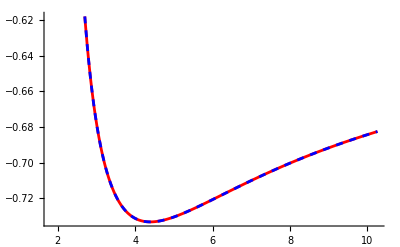

```mathematica
Show[Plot[corrHom["δvϕpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->Red],Plot[corrNearHom["δvϕpar"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->{Blue,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Precession phase.  It diverges at the periastron.

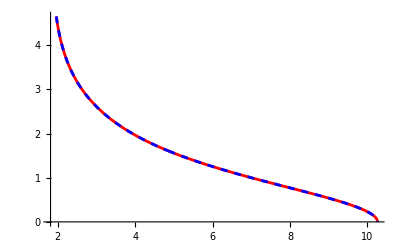

```mathematica
Show[Plot[corrHom["ψp"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->Red],Plot[corrNearHom["ψp"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->{Blue,Dashed}]]
```

Spin correction to the polar motion.  It diverges at the periastron.

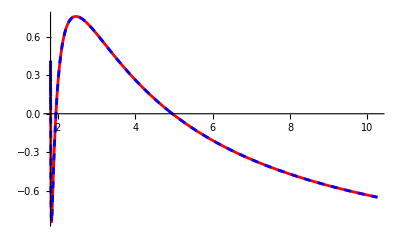

```mathematica
Show[Plot[corrHom["δzort"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->Red],Plot[corrNearHom["δzort"][r],{r,pCritical/(1-eccPlunge),pCritical/(1+eccPlunge)},PlotStyle->{Blue,Dashed}]]
```

## Plunge related to periodic orbits

IMPORTANT NOTE:The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlungeBoundOrbit=0.9`55;
eccPlungeBoundOrbit=0.7`55;
```

```mathematica
pPlungeBoundOrbit=KerrGeoSeparatrix[aPlungeBoundOrbit,eccPlungeBoundOrbit,1]+1;
```

### Calculation orbits

```mathematica
AbsoluteTiming[corrPlungeBoundOrbit=KerrNearEqSpinOrbitCorrFEPlungeBoundOrbit[aPlungeBoundOrbit,pPlungeBoundOrbit,eccPlungeBoundOrbit,1];]
```

{0.002692,Null}

Starting point of plunges related to bound orbits: r_(3g)=2/(1-E_g^2)-(r_(1g)+r_(2g))

```mathematica
r3gPlungeBoundOrbit=2/(1-corrPlungeBoundOrbit["Eg"]^2)-(pPlungeBoundOrbit/(1-eccPlungeBoundOrbit)+pPlungeBoundOrbit/(1+eccPlungeBoundOrbit));
```

### Constants of motion and frequencies

```mathematica
{corrPlungeBoundOrbit["Eg"],corrPlungeBoundOrbit["Lzg"]}
```

{0.941199639071917186567942897662662212751584127805865,2.5339344715101502967956271854830889644265288910007}

BL azimuthal frequency  Ω_ϕ

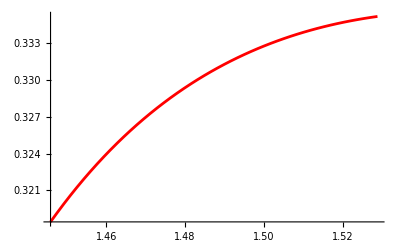

```mathematica
Plot[corrPlungeBoundOrbit["BLFrequenciesGeo"][r],{r,1+√(1-aPlungeBoundOrbit^2)+1/100,r3gPlungeBoundOrbit},PlotStyle->Red,PlotRange->All]
```

BL precession frequency Ω_p

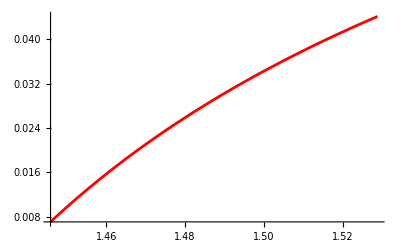

```mathematica
Plot[corrPlungeBoundOrbit["BLPrecessionFrequency"][r],{r,1+√(1-aPlungeBoundOrbit^2)+1/100,r3gPlungeBoundOrbit},PlotStyle->Red,PlotRange->All]
```

### Shifts constants of motion

```mathematica
{corrPlungeBoundOrbit["Es"],corrPlungeBoundOrbit["Jzs"]}
```

{-0.01381515477075871409750072205223024200458700159,0.3791859468714026286322989949746750248038604672}

### Shift frequency

Spin correction BL azimuthal frequency  Ω_ϕ

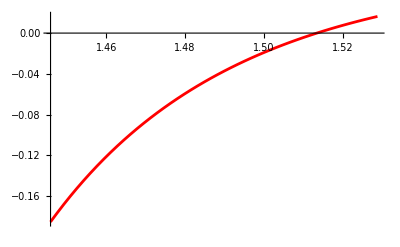

```mathematica
Plot[corrPlungeBoundOrbit["BLFrequenciesCorrection"][r],{r,1+√(1-aPlungeBoundOrbit^2)+1/100,r3gPlungeBoundOrbit},PlotStyle->Red,PlotRange->All]
```

### Geodesic coordinate time and azimuthal trajectories

The coordinate time and azimuthal trajectories diverge logarithmically at the outer (inner) horizons r_+ (r_-).

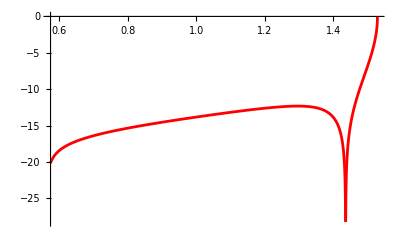

```mathematica
Plot[corrPlungeBoundOrbit["trg"][r],{r,1-√(1-aPlungeBoundOrbit^2)+1/100,r3gPlungeBoundOrbit},PlotStyle->Red,PlotRange->All]
```

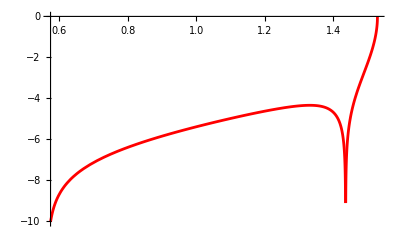

```mathematica
Plot[corrPlungeBoundOrbit["ϕrg"][r],{r,1-√(1-aPlungeBoundOrbit^2)+1/100,r3gPlungeBoundOrbit},PlotStyle->Red,PlotRange->All]
```

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

Note: the correction to the radial motion, δr(r_g),  diverges as a pole at r_g=0.

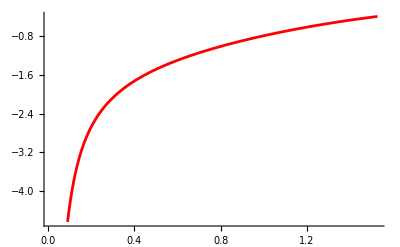

```mathematica
Plot[corrPlungeBoundOrbit["δrpar"][r],{r,1/100,r3gPlungeBoundOrbit},PlotStyle->Red]
```

#### Spin corrections to the radial velocity

Note: the shift to the radial velocity, dδr/dλ,  diverges as a pole  at r_g=0.

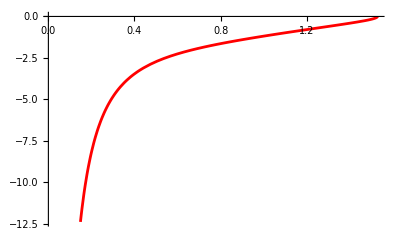

```mathematica
Plot[corrPlungeBoundOrbit["δvrpar"][r],{r,1/100,r3gPlungeBoundOrbit},PlotStyle->Red]
```

#### Spin corrections to the coordinate time and azimuthal trajectories

The shifts to the coordinate time and azimuthal trajectories diverge as poles at the outer (inner) horizons r_+ (r_-), and at r_g=0.

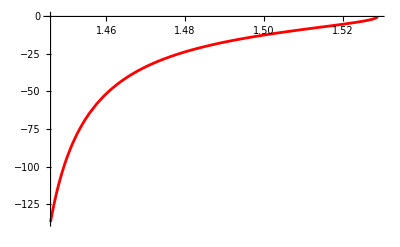

```mathematica
Plot[corrPlungeBoundOrbit["δtpar"][r],{r,1+√(1-aPlungeBoundOrbit^2)+1/100,r3gPlungeBoundOrbit},PlotStyle->Red,PlotRange->All]
```

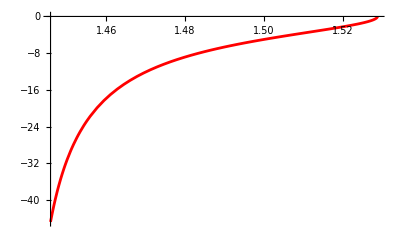

```mathematica
Plot[corrPlungeBoundOrbit["δϕpar"][r],{r,1+√(1-aPlungeBoundOrbit^2)+1/100,r3gPlungeBoundOrbit},PlotStyle->Red]
```

#### Spin corrections to the coordinate time and azimuthal velocities

Note: the shift to the coordinate time, dδt/dλ, and azimuthal velocities,dδϕ/dλ, diverge as poles at the outer (inner) horizons r_+ (r_-), and at r_g=0.

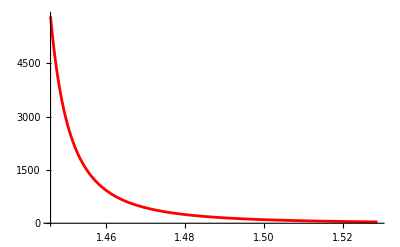

```mathematica
Plot[corrPlungeBoundOrbit["δvtpar"][r],{r,1+√(1-aPlungeBoundOrbit^2)+1/100,r3gPlungeBoundOrbit},PlotStyle->Red,PlotRange->All]
```

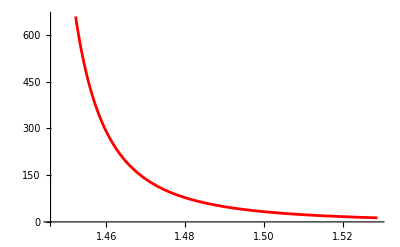

```mathematica
Plot[corrPlungeBoundOrbit["δvϕpar"][r],{r,1+√(1-aPlungeBoundOrbit^2)+1/100,r3gPlungeBoundOrbit},PlotStyle->Red]
```

### Spin corrections orthogonal component of the spin

Precession phase

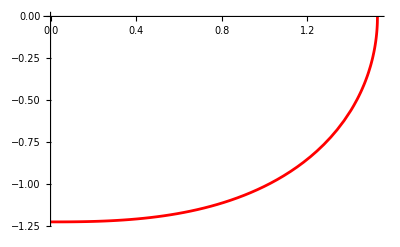

```mathematica
Plot[corrPlungeBoundOrbit["ψp"][r],{r,0,r3gPlungeBoundOrbit},PlotStyle->Red]
```

Spin correction to the polar motion. It diverges as a pole at r_g=0.

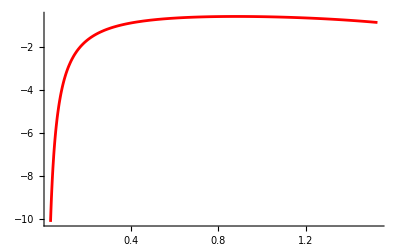

```mathematica
Plot[corrPlungeBoundOrbit["δzort"][r],{r,1/30,r3gPlungeBoundOrbit},PlotStyle->Red,PlotRange->All]
```

## Plunge related to periodic orbits - double root

IMPORTANT NOTE:The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlungeBoundOrbitDoubleRoot=0.9`55;
eccPlungeBoundOrbitDoubleRoot=0;
```

```mathematica
pPlungeBoundOrbitDoubleRoot=KerrGeoSeparatrix[aPlungeBoundOrbitDoubleRoot,0,1]+2;
```

### Calculation orbits

```mathematica
AbsoluteTiming[corrPlungeBoundOrbitDoubleRoot=KerrNearEqSpinOrbitCorrFEPlungeBoundOrbitDoubleRoot[aPlungeBoundOrbitDoubleRoot,pPlungeBoundOrbitDoubleRoot,1];]
```

{0.001624,Null}

```mathematica
AbsoluteTiming[corrNearPlungeBoundOrbitDoubleRoot=KerrNearEqSpinOrbitCorrFEPlungeBoundOrbit[aPlungeBoundOrbitDoubleRoot,pPlungeBoundOrbitDoubleRoot,10^(-10),1];]
```

{0.002722,Null}

```mathematica
r3gPlungeBoundOrbitDoubleRoot=2/(1-corrPlungeBoundOrbitDoubleRoot["Eg"]^2)-2pPlungeBoundOrbitDoubleRoot;
```

### Constants of motion and frequencies

```mathematica
{corrPlungeBoundOrbitDoubleRoot["Eg"],corrPlungeBoundOrbitDoubleRoot["Lzg"]}
```

{0.8958756813167861228765074346035023558150058044699341,2.46310006636593147617693691254920442076726160724309}

```mathematica
{corrNearPlungeBoundOrbitDoubleRoot["Eg"],corrNearPlungeBoundOrbitDoubleRoot["Lzg"]}
```

{0.8958756813167861228774501976595613958360781281237034,2.46310006636593147617913421070621037048766783059906}

BL azimuthal frequency  Ω_ϕ

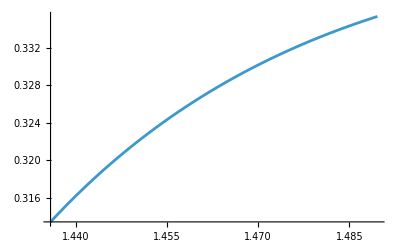

```mathematica
Plot[corrPlungeBoundOrbitDoubleRoot["BLFrequenciesGeo"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2),r3gPlungeBoundOrbitDoubleRoot}]
```

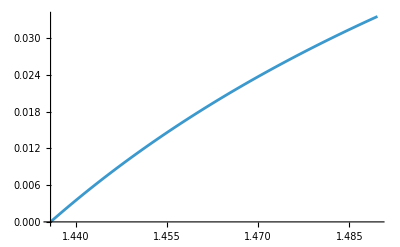

```mathematica
Plot[corrPlungeBoundOrbitDoubleRoot["BLPrecessionFrequency"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2),r3gPlungeBoundOrbitDoubleRoot}]
```

### Shifts constants of motion

```mathematica
{corrPlungeBoundOrbitDoubleRoot["Es"],corrPlungeBoundOrbitDoubleRoot["Jzs"]}
```

{-0.0215150329754180592529697598837321058924993740122,0.4988052790331831303291111862338487818633092363501}

```mathematica
{corrNearPlungeBoundOrbitDoubleRoot["Es"],corrNearPlungeBoundOrbitDoubleRoot["Jzs"]}
```

{-0.0215150329760486027201014620495255434564660807099,0.498805279026952286059296344895391920617912352906}

### Shift frequency

Spin correction BL azimuthal frequency  Ω_ϕ

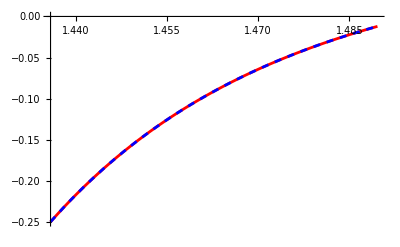

```mathematica
Show[Plot[corrPlungeBoundOrbitDoubleRoot["BLFrequenciesCorrection"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2),r3gPlungeBoundOrbitDoubleRoot},PlotStyle->Red],Plot[corrNearPlungeBoundOrbitDoubleRoot["BLFrequenciesCorrection"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2),r3gPlungeBoundOrbitDoubleRoot},PlotStyle->{Blue,Dashed},WorkingPrecision->22]]
```

### Geodesic coordinate time and azimuthal trajectories

The coordinate time and azimuthal trajectories diverge logarithmically  at the outer (inner) horizons r_+ (r_-)

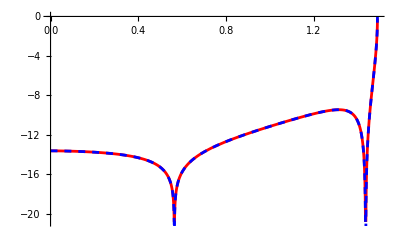

```mathematica
Show[Plot[corrPlungeBoundOrbitDoubleRoot[ "trg"][r],{r,0,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->Red],Plot[corrNearPlungeBoundOrbitDoubleRoot[ "trg"][r],{r,0,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->{Blue,Dashed},WorkingPrecision->40]]
```

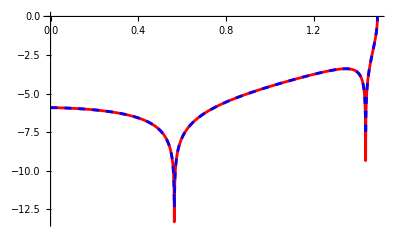

```mathematica
Show[Plot[corrPlungeBoundOrbitDoubleRoot[ "ϕrg"][r],{r,0,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->Red],Plot[corrNearPlungeBoundOrbitDoubleRoot[ "ϕrg"][r],{r,0,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->{Blue,Dashed},WorkingPrecision->20]]
```

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

Note: the correction to the radial motion, δr(r_g),  diverge as a poles at r_g=0.

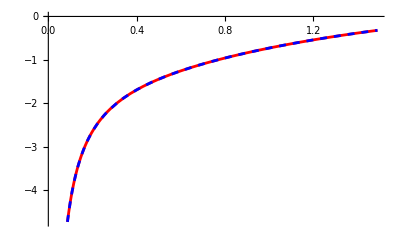

```mathematica
Show[Plot[corrPlungeBoundOrbitDoubleRoot["δrpar"][r],{r,1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->Red],Plot[corrNearPlungeBoundOrbitDoubleRoot["δrpar"][r],{r,1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->{Blue,Dashed},WorkingPrecision->22]]
```

#### Spin corrections to the radial velocity

Note: the shift to the radial velocity, dδr/dλ, diverges as a pole at r_g=0.

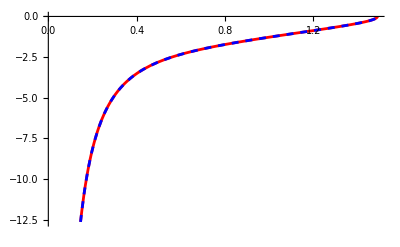

```mathematica
Show[Plot[corrPlungeBoundOrbitDoubleRoot["δvrpar"][r],{r,1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->Red],Plot[corrNearPlungeBoundOrbitDoubleRoot["δvrpar"][r],{r,1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->{Blue,Dashed}]]
```

#### Spin corrections to the coordinate time and azimuthal trajectories

The shifts to the coordinate time and azimuthal trajectories diverge as poles at the outer (inner) horizons r_+ (r_-), and at r_g=0.

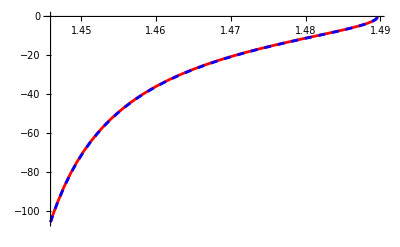

```mathematica
Show[Plot[corrPlungeBoundOrbitDoubleRoot["δtpar"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2)+1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->Red],Plot[corrNearPlungeBoundOrbitDoubleRoot["δtpar"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2)+1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->{Blue,Dashed},WorkingPrecision->20]]
```

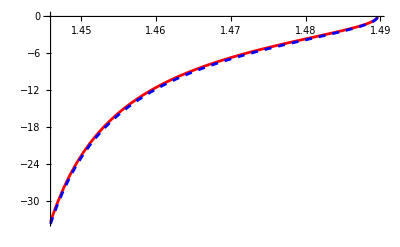

```mathematica
Show[Plot[corrPlungeBoundOrbitDoubleRoot["δϕpar"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2)+1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->Red],Plot[corrNearPlungeBoundOrbitDoubleRoot["δϕpar"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2)+1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->{Blue,Dashed},WorkingPrecision->20]]
```

#### Spin corrections to the coordinate time and azimuthal velocities

Note: the shift to the coordinate time, dδt/dλ, and azimuthal velocities,dδϕ/dλ,  diverge as poles at the outer (inner) horizons r_+ (r_-), and at r_g=0.

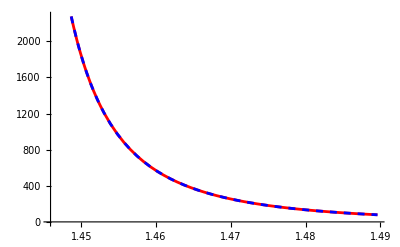

```mathematica
Show[Plot[corrPlungeBoundOrbitDoubleRoot["δvtpar"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2)+1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->Red],Plot[corrNearPlungeBoundOrbitDoubleRoot["δvtpar"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2)+1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->{Blue,Dashed}]]
```

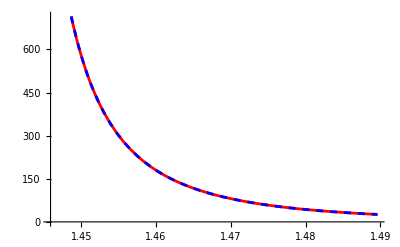

```mathematica
Show[Plot[corrPlungeBoundOrbitDoubleRoot["δvϕpar"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2)+1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->Red],Plot[corrNearPlungeBoundOrbitDoubleRoot["δvϕpar"][r],{r,1+√(1-aPlungeBoundOrbitDoubleRoot^2)+1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->{Blue,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Precession phase

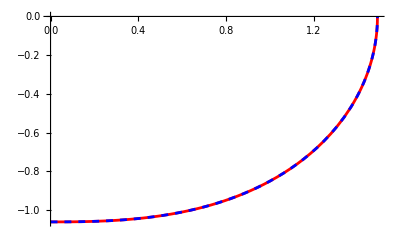

```mathematica
Show[Plot[corrPlungeBoundOrbitDoubleRoot["ψp"][r],{r,0,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->Red],Plot[corrNearPlungeBoundOrbitDoubleRoot["ψp"][r],{r,0,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->{Blue,Dashed},WorkingPrecision->22]]
```

Spin correction to the polar motion. It diverges as a pole at r_g=0

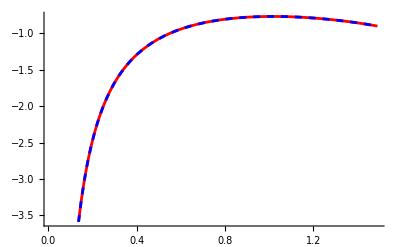

```mathematica
Show[Plot[corrPlungeBoundOrbitDoubleRoot["δzort"][r],{r,1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->Red],Plot[corrNearPlungeBoundOrbitDoubleRoot["δzort"][r],{r,1/100,r3gPlungeBoundOrbitDoubleRoot},PlotStyle->{Blue,Dashed},WorkingPrecision->22]]
```

## Critical plunge and homoclinic orbits

IMPORTANT NOTE:The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aCritplunge=0.9`55;
eccCritplunge=0.45`55;
```

```mathematica
pCritplunge=KerrGeoSeparatrix[aCritplunge,eccCritplunge,1]
```

2.7743315642164893578740640805413320785590353773155034

### Calculation orbits

Critical plunge

```mathematica
AbsoluteTiming[corrCritplunge=KerrNearEqSpinOrbitCorrFECritPlunge[aCritplunge,pCritplunge,eccCritplunge,1];]
```

{0.00228,Null}

Homoclinic orbits

```mathematica
AbsoluteTiming[corrHom=KerrNearEqSpinOrbitCorrFEHom[aCritplunge,pCritplunge,eccCritplunge,1];]
```

{0.007842,Null}

### Constants of motion and frequencies

```mathematica
{corrCritplunge["Eg"],corrCritplunge["Lzg"]}
```

{0.8800817122061824181861312153403801042527660746204284,2.2348673551008968966337980539401664889731519909096}

BL azimuthal frequency  Ω_ϕ

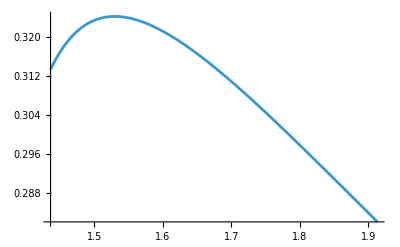

```mathematica
Plot[corrCritplunge["BLFrequenciesGeo"][r],{r,1+√(1-aCritplunge^2),pCritplunge/(1+eccCritplunge)}]
```

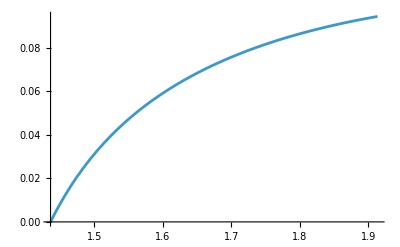

```mathematica
Plot[corrCritplunge["BLPrecessionFrequency"][r],{r,1+√(1-aCritplunge^2),pCritplunge/(1+eccCritplunge)}]
```

### Shifts constants of motion

```mathematica
{corrCritplunge["Es"],corrCritplunge["Jzs"]}
```

{-0.0656945531905828443918811784544166175292592653791,0.10193711072260476871328449729981989878643438115}

### Shifts frequency

BL frequencies. Order of appearance:   Ω_ϕ

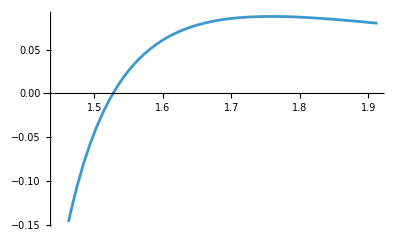

```mathematica
Plot[corrCritplunge["BLFrequenciesCorrection"][r],{r,1+√(1-aCritplunge^2),pCritplunge/(1+eccCritplunge)}]
```

### Geodesic trajectories

The coordinate time and azimuthal trajectories diverge logarithmically at the periastron

```mathematica
{corrCritplunge[ "trg"][pCritplunge/(1+eccCritplunge)],corrCritplunge[ "ϕrg"][pCritplunge/(1+eccCritplunge)]}
```

{Indeterminate,Indeterminate}

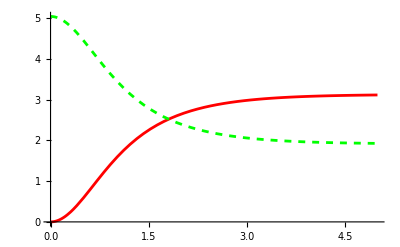

```mathematica
Show[Plot[corrCritplunge[ "rg"][λ],{λ,0,5},PlotStyle->Red,PlotRange->All],Plot[corrHom[ "rg"][λ],{λ,0,5},PlotRange->All,PlotStyle->{Green,Dashed}]]
```

Comparison radial velocity homoclinic orbit and critical plunge. Both type of motion can be represent by the same function.

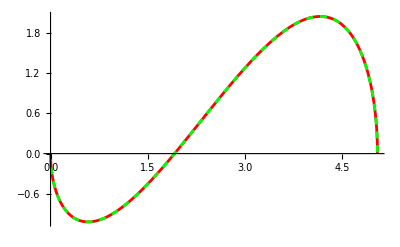

```mathematica
Show[Plot[corrCritplunge[ "vrg"][r],{r,0,pCritplunge/(1-eccCritplunge)},PlotStyle->Red],Plot[corrHom[ "vrg"][r],{r,0,pCritplunge/(1-eccCritplunge)},PlotStyle->{Green,Dashed}]]
```

Comparison coordinate time and azimuthal trajectories. Homoclinic orbits have a different sign than critical plunges. Notice that both trajectories diverge logarithmically at the outer (inner) horizon r_+(r_-)

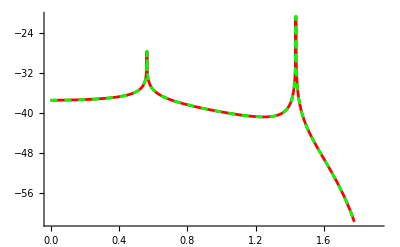

```mathematica
Show[Plot[corrCritplunge[ "trg"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->Red],Plot[-corrHom[ "trg"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->{Green,Dashed}]]
```

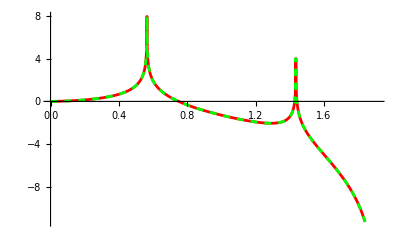

```mathematica
Show[Plot[corrCritplunge[ "ϕrg"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->Red],Plot[-corrHom[ "ϕrg"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->{Green,Dashed}]]
```

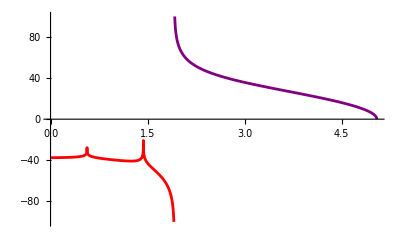

```mathematica
Show[Plot[corrCritplunge[ "trg"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->Red,PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-100,100}}],Plot[corrHom[ "trg"][r],{r,pCritplunge/(1+eccCritplunge),pCritplunge/(1-eccCritplunge)},PlotStyle->{Purple},PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-100,100}}]]
```

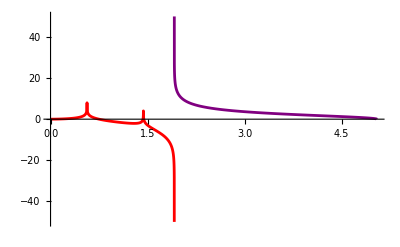

```mathematica
Show[Plot[corrCritplunge[ "ϕrg"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->Red,PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-50,50}}],Plot[corrHom[ "ϕrg"][r],{r,pCritplunge/(1+eccCritplunge),pCritplunge/(1-eccCritplunge)},PlotStyle->{Purple},PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-50,50}}]]
```

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

Note: the correction to the radial motion, δr(r_g), is  defined at r_g=r_(2g) only if they are parametrized using the Mino-time λ.  δr(r_g) is not defined at when parametrized using the geodesic radial coordinate r_g. However,  δr(r_g) is finite in the limit r_g->r_(2g)

The correction to the radial motion is finite near the periastron

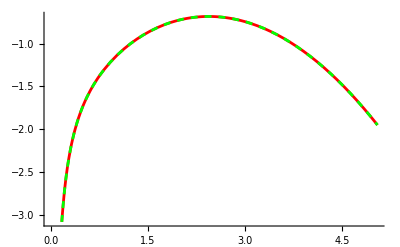

```mathematica
Show[Plot[corrCritplunge[ "δrpar"][r],{r,0,pCritplunge/(1-eccCritplunge)},PlotStyle->Red],Plot[corrHom[  "δrpar"][r],{r,0,pCritplunge/(1-eccCritplunge)},PlotStyle->{Green,Dashed}]]
```

#### Spin corrections to the radial velocity

Note: the shift to the radial velocity, dδr/dλ, is defined at r_g=r_(2g) only if it is parametrized using the Mino-time λ. dδr/dλ is not defined at  r_g=r_(2g) when parametrized using the geodesic radial coordinate r_g. However, dδr/dλ is finite in the limit r_g->r_(2g)

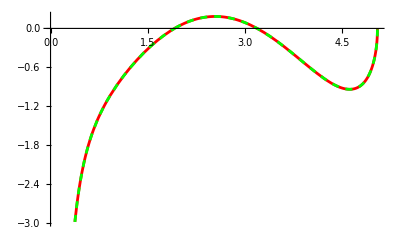

```mathematica
Show[Plot[corrCritplunge[ "δvrpar"][r],{r,0,pCritplunge/(1-eccCritplunge)},PlotStyle->Red],Plot[corrHom[  "δvrpar"][r],{r,0,pCritplunge/(1-eccCritplunge)},PlotStyle->{Green,Dashed}]]
```

#### Spin corrections to the coordinate time and azimuthal trajectories

The shifts to the coordinate time and azimuthal trajectories diverge logarithmically at the periastron, as the corresponding geodesic trajectories, while  diverging as poles at the outer (inner) horizons r_+ (r_-), and at r_g=0.

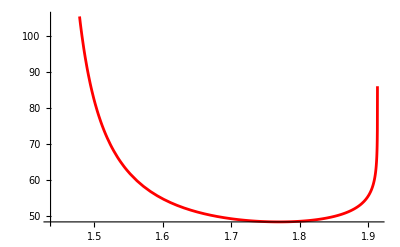

```mathematica
Plot[corrCritplunge["δtpar"][r],{r,1+√(1-aCritplunge^2),pCritplunge/(1+eccCritplunge)-10^(-5)},PlotStyle->Red]
```

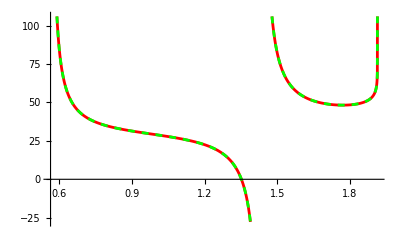

```mathematica
Show[Plot[corrCritplunge[ "δtpar"][r],{r,1-√(1-aCritplunge^2),pCritplunge/(1+eccCritplunge)},PlotStyle->Red],Plot[-corrHom[ "δtpar"][r],{r,1-√(1-aCritplunge^2),pCritplunge/(1+eccCritplunge)},PlotStyle->{Green,Dashed}]]
```

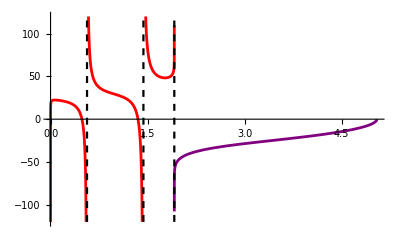

```mathematica
Show[Plot[corrCritplunge[ "δtpar"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->Red,PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-120,120}}],Plot[corrHom[  "δtpar"][r],{r,pCritplunge/(1+eccCritplunge),pCritplunge/(1-eccCritplunge)},PlotStyle->{Purple},PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-120,120}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{pCritplunge/(1+eccCritplunge),-120},{pCritplunge/(1+eccCritplunge),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aCritplunge^2),-120},{1+√(1-aCritplunge^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aCritplunge^2),-120},{1-√(1-aCritplunge^2),120}}]}]]
```

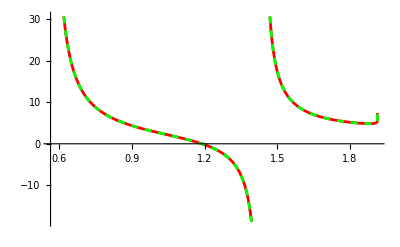

```mathematica
Show[Plot[corrCritplunge[ "δϕpar"][r],{r,1-√(1-aCritplunge^2),pCritplunge/(1+eccCritplunge)},PlotStyle->Red],Plot[-corrHom[  "δϕpar"][r],{r,1-√(1-aCritplunge^2),pCritplunge/(1+eccCritplunge)},PlotStyle->{Green,Dashed}]]
```

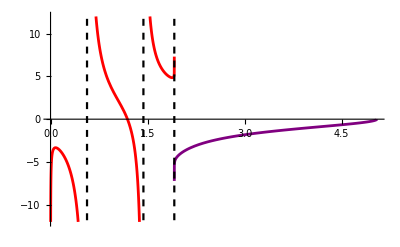

```mathematica
Show[Plot[corrCritplunge[ "δϕpar"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->Red,PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-12,12}}],Plot[corrHom[  "δϕpar"][r],{r,pCritplunge/(1+eccCritplunge),pCritplunge/(1-eccCritplunge)},PlotStyle->{Purple},PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-12,12}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{pCritplunge/(1+eccCritplunge),-120},{pCritplunge/(1+eccCritplunge),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aCritplunge^2),-120},{1+√(1-aCritplunge^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aCritplunge^2),-120},{1-√(1-aCritplunge^2),120}}]}]]
```

#### Spin corrections to the coordinate time and azimuthal velocities

Note: the shift to the coordinate time, dδt/dλ, and azimuthal velocities,dδϕ/dλ,  diverge as poles at the outer (inner) horizons r_+ (r_-), and at r_g=0.

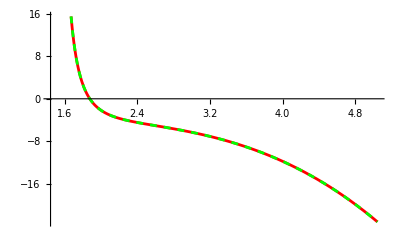

```mathematica
Show[Plot[corrCritplunge[ "δvtpar"][r],{r,1+√(1-aCritplunge^2)+1/100,pCritplunge/(1-eccCritplunge)},PlotStyle->Red],Plot[corrHom[ "δvtpar"][r],{r,1+√(1-aCritplunge^2)+1/100,pCritplunge/(1-eccCritplunge)},PlotStyle->{Green,Dashed}]]
```

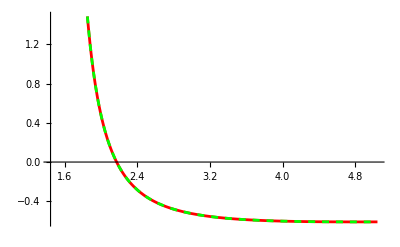

```mathematica
Show[Plot[corrCritplunge[ "δvϕpar"][r],{r,1+√(1-aCritplunge^2)+1/100,pCritplunge/(1-eccCritplunge)},PlotStyle->Red],Plot[corrHom[ "δvϕpar"][r],{r,1+√(1-aCritplunge^2)+1/100,pCritplunge/(1-eccCritplunge)},PlotStyle->{Green,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Precession phase. It diverges logarithmically at the periastron

```mathematica
{corrCritplunge["ψp"][0],corrCritplunge["ψp"][pCritplunge/(1+eccCritplunge)]}
```

{0.,Indeterminate}

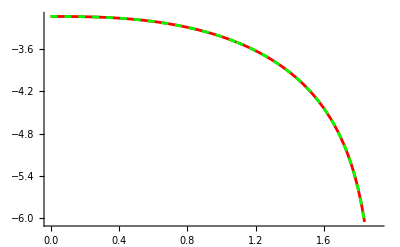

```mathematica
Show[Plot[corrCritplunge[ "ψp"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->Red],Plot[-corrHom["ψp"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->{Green,Dashed}]]
```

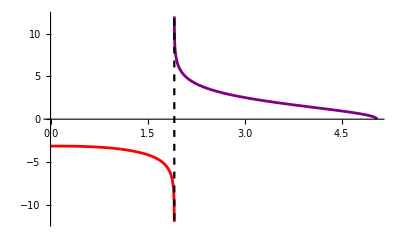

```mathematica
Show[Plot[corrCritplunge[ "ψp"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->Red,PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-12,12}}],Plot[corrHom[ "ψp"][r],{r,pCritplunge/(1+eccCritplunge),pCritplunge/(1-eccCritplunge)},PlotStyle->{Purple},PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-12,12}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{pCritplunge/(1+eccCritplunge),-120},{pCritplunge/(1+eccCritplunge),120}}]}]]
```

Spin correction to the polar motion. It diverges as a pole at r_g=0 and logarithmically at the periastron.

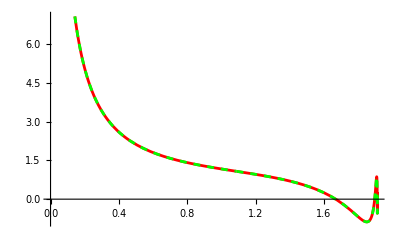

```mathematica
Show[Plot[corrCritplunge[ "δzort"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->Red],Plot[corrHom[  "δzort"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->{Green,Dashed}]]
```

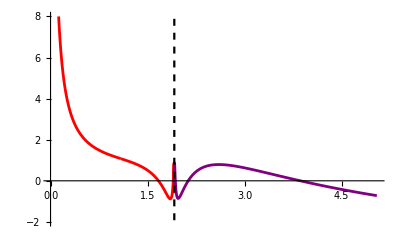

```mathematica
Show[Plot[corrCritplunge[ "δzort"][r],{r,0,pCritplunge/(1+eccCritplunge)},PlotStyle->Red,PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-2,8}}],Plot[corrHom[  "δzort"][r],{r,pCritplunge/(1+eccCritplunge),pCritplunge/(1-eccCritplunge)},PlotStyle->{Purple},PlotRange->{{0,pCritplunge/(1-eccCritplunge)+1/100},{-2,8}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{pCritplunge/(1+eccCritplunge),-120},{pCritplunge/(1+eccCritplunge),120}}]}]]
```

## ISCO plunge

IMPORTANT NOTE:The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aISCOplunge=0.9`55;
```

Geodesic ISCO radius

```mathematica
pISCOplunge=KerrGeoSeparatrix[aISCOplunge,0,1]
```

2.3208830417618872467900861919226860889786023247688005

### Calculation orbits

```mathematica
AbsoluteTiming[corrISCOplunge=KerrNearEqSpinOrbitCorrFEISCOPlunge[aISCOplunge,1];]
```

{0.000827,Null}

```mathematica
AbsoluteTiming[corrNearISCOplunge=KerrNearEqSpinOrbitCorrFECritPlunge[aISCOplunge,pISCOplunge,10^(-6),1];]
```

{0.003416,Null}

### Constants of motion and frequencies

```mathematica
{corrISCOplunge["Eg"],corrISCOplunge["Lzg"]}
```

{0.84424700800553600052360803166940605759191293560462162,2.099784756123845457483589423597379022975460469494319}

```mathematica
{corrNearISCOplunge["Eg"],corrNearISCOplunge["Lzg"]}
```

{0.8442470080056903447356002105055995399646720209496528,2.09978475612453008772698887150942089377120028189009}

BL azimuthal frequency  Ω_ϕ

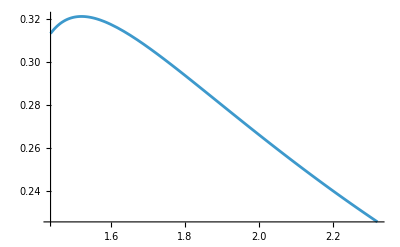

```mathematica
Plot[corrISCOplunge["BLFrequenciesGeo"][r],{r,1+√(1-aISCOplunge^2),pISCOplunge}]
```

BL precession frequency  Ω_p

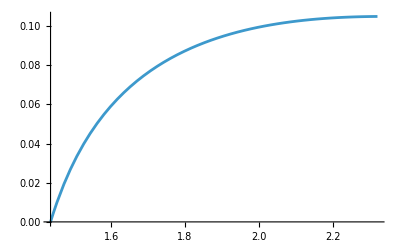

```mathematica
Plot[corrISCOplunge["BLPrecessionFrequency"][r],{r,1+√(1-aISCOplunge^2),pISCOplunge}]
```

### Shifts constants of motion

```mathematica
{corrISCOplunge["Es"],corrISCOplunge["Jzs"]}
```

{-0.107184716148375331318647405147804275845968248634594,-0.01017304709128464742500977708270985228620850934787}

```mathematica
{corrNearISCOplunge["Es"],corrNearISCOplunge["Jzs"]}
```

{-0.1071847161481312795825509292559519783766746945334,-0.010173047090486330675492761089772540487626133263}

### Shifts frequency

BL frequencies. Order of appearance:   Ω_ϕ

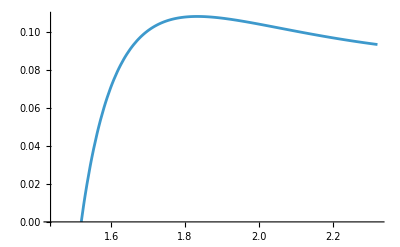

```mathematica
Plot[corrISCOplunge["BLFrequenciesCorrection"][r],{r,1+√(1-aISCOplunge^2),pISCOplunge}]
```

### Geodesic coordinate time and azimuthal trajectories

The coordinate time and azimuthal trajectories diverge logarithmically at  diverge at the outer (inner) horizons r_+ (r_-).

```mathematica
{corrISCOplunge[ "trg"][pISCOplunge],corrISCOplunge[ "ϕrg"][pISCOplunge]}
```

{-3.×10^27,-8.×10^26}

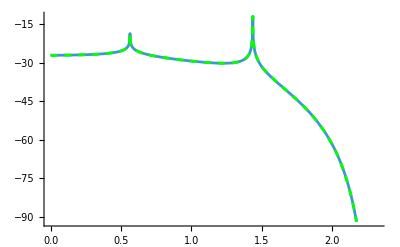

```mathematica
Show[Plot[corrISCOplunge[ "trg"][r],{r,0,pISCOplunge}],Plot[corrNearISCOplunge[ "trg"][r],{r,0,pISCOplunge},PlotStyle->{Green,Dashed}]]
```

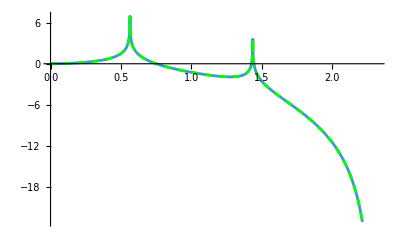

```mathematica
Show[Plot[corrISCOplunge[ "ϕrg"][r],{r,0,pISCOplunge}],Plot[corrNearISCOplunge[ "ϕrg"][r],{r,0,pISCOplunge},PlotStyle->{Green,Dashed}]]
```

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

Note: the correction to the radial motion, δr(r_g),  diverges at r_g=0.

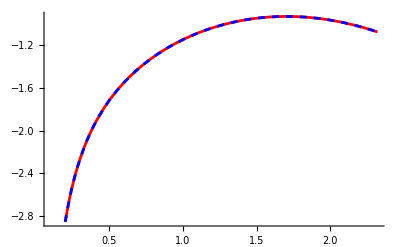

```mathematica
Show[Plot[corrISCOplunge["δrpar"][r],{r,1/10,pISCOplunge},PlotStyle->Red],Plot[corrNearISCOplunge["δrpar"][r],{r,1/10,pISCOplunge},PlotStyle->{Blue,Dashed}]]
```

#### Spin corrections to the radial velocity

Note: the shift to the radial velocity, dδr/dλ, diverges at r_g=0.

```mathematica
corrISCOplunge["δvrpar"][pISCOplunge-10^(-20)]
```

2.2595837265×10^-31

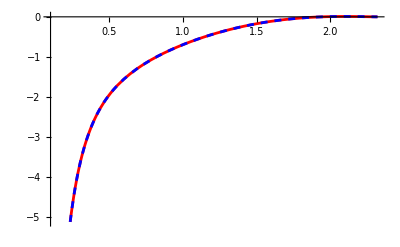

```mathematica
Show[Plot[corrISCOplunge["δvrpar"][r],{r,1/10,pISCOplunge},PlotStyle->Red],Plot[corrNearISCOplunge["δvrpar"][r],{r,1/10,pISCOplunge},PlotStyle->{Blue,Dashed}]]
```

#### Spin corrections to the coordinate time and azimuthal trajectories

The shifts to the coordinate time and azimuthal trajectories diverge as poles at the geodesics ISCO, at the outer (inner) horizons r_+ (r_-), and at r=0.

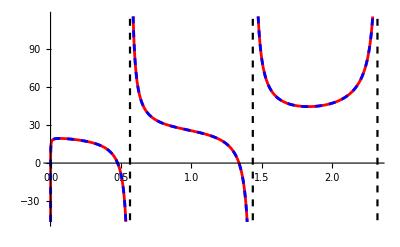

```mathematica
Show[Plot[corrISCOplunge["δtpar"][r],{r,0,pISCOplunge},PlotStyle->Red],Plot[corrNearISCOplunge["δtpar"][r],{r,0,pISCOplunge},PlotStyle->{Blue,Dashed}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{pISCOplunge,-120},{pISCOplunge,120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aISCOplunge^2),-120},{1+√(1-aISCOplunge^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aISCOplunge^2),-120},{1-√(1-aISCOplunge^2),120}}]}]]
```

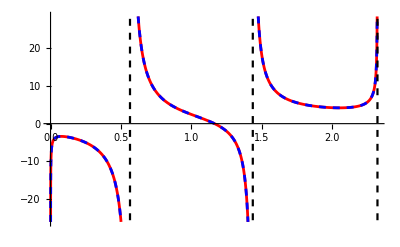

```mathematica
Show[Plot[corrISCOplunge["δϕpar"][r],{r,0,pISCOplunge},PlotStyle->Red],Plot[corrNearISCOplunge["δϕpar"][r],{r,0,pISCOplunge},PlotStyle->{Blue,Dashed}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{pISCOplunge,-120},{pISCOplunge,120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aISCOplunge^2),-120},{1+√(1-aISCOplunge^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aISCOplunge^2),-120},{1-√(1-aISCOplunge^2),120}}]}]]
```

#### Spin corrections to the coordinate time and azimuthal velocities

Note: the shift to the coordinate time, dδt/dλ, and azimuthal velocities,dδϕ/dλ,  diverge as poles at the outer (inner) horizons r_+ (r_-), and at r=0.

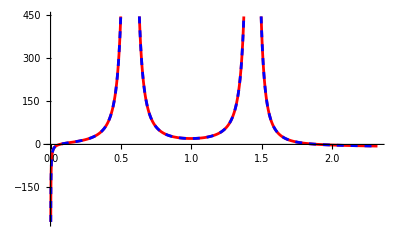

```mathematica
Show[Plot[corrISCOplunge["δvtpar"][r],{r,0,pISCOplunge},PlotStyle->Red],Plot[corrNearISCOplunge["δvtpar"][r],{r,0,pISCOplunge},PlotStyle->{Blue,Dashed}]]
```

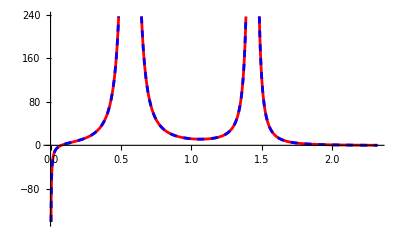

```mathematica
Show[Plot[corrISCOplunge["δvϕpar"][r],{r,0,pISCOplunge},PlotStyle->Red],Plot[corrNearISCOplunge["δvϕpar"][r],{r,0,pISCOplunge},PlotStyle->{Blue,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Precession phase.  It diverges as a pole at the geodesic ISCO.

```mathematica
{corrISCOplunge["ψp"][0],corrISCOplunge["ψp"][pISCOplunge]}
```

{0.,-4.×10^26}

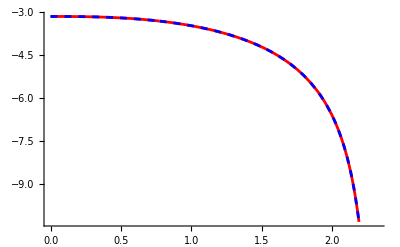

```mathematica
Show[Plot[corrISCOplunge["ψp"][r],{r,0,pISCOplunge},PlotStyle->Red],Plot[corrNearISCOplunge["ψp"][r],{r,0,pISCOplunge},PlotStyle->{Blue,Dashed}]]
```

```mathematica
corrISCOplunge["ψp"][pISCOplunge]
```

-4.×10^26

Spin correction to the polar motion

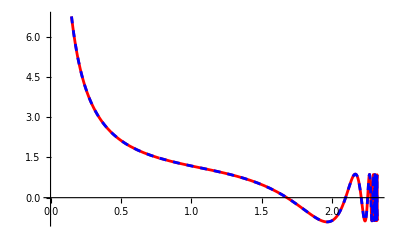

```mathematica
Show[Plot[corrISCOplunge["δzort"][r],{r,0,pISCOplunge},PlotStyle->Red],Plot[corrNearISCOplunge["δzort"][r],{r,0,pISCOplunge},PlotStyle->{Blue,Dashed}]]
```

## Example calculation shift Innermost Bound Circular Orbit

```mathematica
δIBCO=KerrNearEqSpinOrbitCorrFEδIBCO[0.9`35, 1];
```

```mathematica
δIBCO
```

<|Eg→1,Lzg→2.632455532033675866399778708886544,Es→0,Jzs→0.2402530733520421479998770604925243,rIBCO→1.732455532033675866399778708886544,δrIBCO→-0.480506146704084295999754120985|>

```mathematica
2δIBCO["δrIBCO"]
```

-0.96101229340816859199950824197

```mathematica
KerrNearEqSpinOrbitCorrFECritPlunge[0.9`65,KerrGeoSeparatrix[0.9`65,1,1],1`65-10^(-15),1]["δp"]
```

-0.961012293408169

Geodesic IBCO from the BHPToolkit

```mathematica
KerrGeoSeparatrix[0.9`65,1`65-10^(-13),1]
```

3.46491106406722011002295573472568481545357524451715090829474566

```mathematica
KerrGeoIBSO[0.9`35, 1]
```

1.732455532033675866399778708886544

## Plots orbits - fixed eccentricity

For plots

```mathematica
Integerise[num_]:=If[Round[num]==num,ToString[Round@num]<>".0",ToString@num]
```

#### Shift IBCO

For plots

```mathematica
Integerise[num_]:=If[Round[num]==num,ToString[Round@num]<>".0",ToString@num]
```

```mathematica
xbibco=Join[Table[{0.05i,,{0.015,0}},{i,0,100}],Table[{0.2i,Integerise[0.2i],{0.03,0}},{i,0,50}]];
```

```mathematica
xlibco=Join[Table[{0.1i,,{0.015,0}},{i,0,100}],Table[{0.5i,Integerise[0.5i],{0.03,0}},{i,0,50}]];
```

```mathematica
listprimaryspin=Join[Table[i,{i,0,0.9,0.1}],{0.95,0.99,0.999,1`65-10^(-10)}];
```

```mathematica
δribcopro=Table[KerrNearEqSpinOrbitCorrFEδIBCO[listprimaryspin[[i]],1]["δrIBCO"],{i,Length[listprimaryspin]}];
```

```mathematica
δribcoret=Table[KerrNearEqSpinOrbitCorrFEδIBCO[listprimaryspin[[i]],-1]["δrIBCO"],{i,Length[listprimaryspin]}];
```

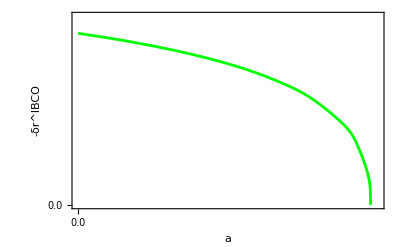

```mathematica
plotδrIBCO=ListPlot[Table[{listprimaryspin[[i]],-δribcopro[[i]]},{i,Length[listprimaryspin]}],Frame->{{True,False},{True,False}},Joined->True,InterpolationOrder->3,PlotStyle->{Green},FrameLabel->{Style["a",Black,21],Style["-δr^IBCO",Black,21]},FrameTicks->{{xlsepFixecc,None},{xbsep,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,1.025},{0,1.1}},ImageMargins->5,ImagePadding->{{60, 10}, {Automatic,10}},ImageSize->400]
```

```mathematica
(*Export["ibco_shift_plot.pdf",plotδrIBCO]*)
```

#### Spin correction plunge from ISCO - equatorial plane

```mathematica
xbISCOplunge=Join[Table[{0.1i,,{0.015,0}},{i,0,100}],Table[{0.5i,Integerise[0.5i],{0.03,0}},{i,0,50}]];
xlδrISCOplunge=Join[Table[{0.25i,,{0.015,0}},{i,-100,0}],Table[{i,Integerise[i],{0.03,0}},{i,-50,0}]];
xlδtISCOplunge=Join[Table[{5i,,{0.015,0}},{i,-100,100}],Table[{20i,Integerise[20i],{0.03,0}},{i,-50,50}]];
xlδϕISCOplunge=Join[Table[{2.5i,,{0.015,0}},{i,-100,100}],Table[{10i,Integerise[10i],{0.03,0}},{i,-50,50}]];
```

```mathematica
aISCOplunge=0.9`55;
```

```mathematica
pISCOplunge=KerrGeoSeparatrix[aISCOplunge,0,1]
```

2.3208830417618872467900861919226860889786023247688005

```mathematica
AbsoluteTiming[corrISCOplunge=KerrNearEqSpinOrbitCorrFEISCOPlunge[aISCOplunge,1];]
```

{0.001071,Null}

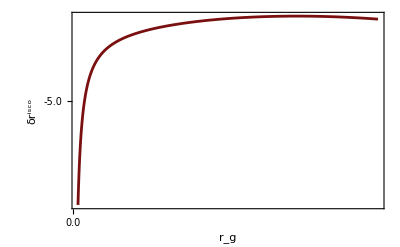

```mathematica
plotδrISCO=Plot[corrISCOplunge["δrpar"][r],{r,0,pISCOplunge},PlotStyle->DarkRed,Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δr^isco",Black,21]},FrameTicks->{{xlδrISCOplunge,None},{xbISCOplunge,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,pISCOplunge},{-1/10,-10}},ImageMargins->10,ImagePadding->{{80, 10}, {Automatic, 10}}]
```

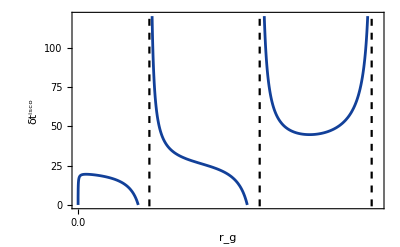

```mathematica
plotδtISCO=Show[Plot[corrISCOplunge["δtpar"][r],{r,0,pISCOplunge},PlotStyle->{DarkBlue},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δt^isco",Black,21]},FrameTicks->{{xlδtISCOplunge,None},{xbISCOplunge,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,pISCOplunge+0.05},{0,120}},ImageMargins->10,ImagePadding->{{80, 10}, {Automatic, 10}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{pISCOplunge,-120},{pISCOplunge,120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aISCOplunge^2),-120},{1+√(1-aISCOplunge^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aISCOplunge^2),-120},{1-√(1-aISCOplunge^2),120}}]}]]
```

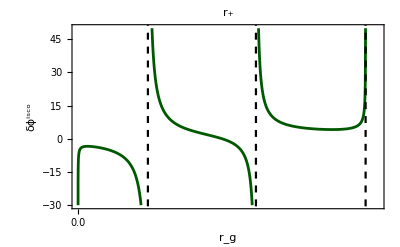

```mathematica
plotδϕISCO=Show[Plot[corrISCOplunge["δϕpar"][r],{r,0,pISCOplunge},PlotStyle->{DarkGreen},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δϕ^isco",Black,21]},FrameTicks->{{xlδϕISCOplunge,None},{xbISCOplunge,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,pISCOplunge+0.1},{-30,50}},ImageMargins->10,ImagePadding->{{80, 10}, {Automatic, 10}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{pISCOplunge,-120},{pISCOplunge,120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aISCOplunge^2),-120},{1+√(1-aISCOplunge^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aISCOplunge^2),-120},{1-√(1-aISCOplunge^2),120}}]}],PlotLabel->"r_+"]
```

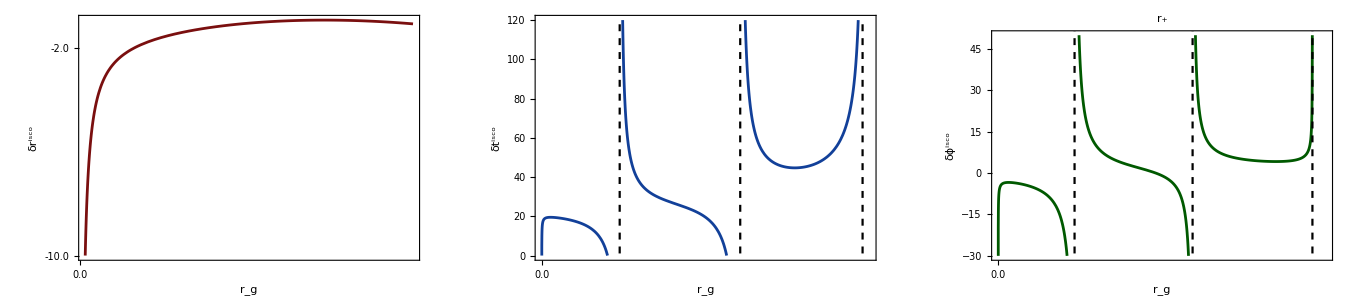

```mathematica
shiftISCOplungeplots=GraphicsRow[{plotδrISCO,plotδtISCO,plotδϕISCO},Spacings->16,ImageSize->1350]
```

```mathematica
(*Export["shift_isco_plunge_plots.pdf",shiftISCOplungeplots]*)
```

shift_isco_plunge_plots.pdf

#### Spin correction generic plunge - equatorial plane

```mathematica
xbgenericplunge=Join[Table[{0.1i,,{0.015,0}},{i,0,100}],Table[{0.5i,Integerise[0.5i],{0.03,0}},{i,0,50}]];
xlδrgenericplunge=Join[Table[{0.25i,,{0.015,0}},{i,-100,0}],Table[{i,Integerise[i],{0.03,0}},{i,-50,0}]];
xlδtgenericplunge=Join[Table[{5i,,{0.015,0}},{i,-100,100}],Table[{25i,Integerise[25i],{0.03,0}},{i,-50,50}]];
xlδϕgenericplunge=Join[Table[{2.5i,,{0.015,0}},{i,-100,100}],Table[{10i,Integerise[10i],{0.03,0}},{i,-50,50}]];
```

```mathematica
aPlunge=0.9`55;
eccPlunge=0.32`55;
```

```mathematica
KerrGeoSeparatrix[aPlunge,eccPlunge,1]
```

2.6270469505690145892193952028064598761326729466885252

```mathematica
pPlunge=2.27`55;
```

```mathematica
r1gPlunge=pPlunge/(1-eccPlunge);
```

```mathematica
AbsoluteTiming[corrPlunge=KerrNearEqSpinOrbitCorrFEPlunge[aPlunge,pPlunge,eccPlunge,1];]
```

{0.001925,Null}

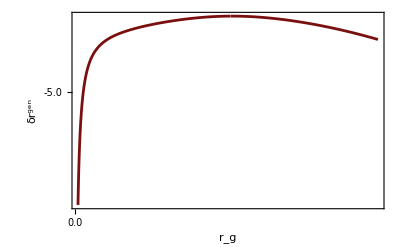

```mathematica
plotδrgeneric=Plot[corrPlunge["δrpar"][r],{r,0,r1gPlunge},PlotStyle->DarkRed,Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δr^gen",Black,21]},FrameTicks->{{xlδrgenericplunge,None},{xbgenericplunge,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,r1gPlunge},{-1,-10}},ImageMargins->10,ImagePadding->{{80, 10}, {Automatic, 10}}]
```

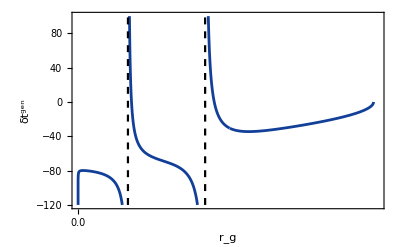

```mathematica
plotδtgeneric=Show[Plot[corrPlunge["δtpar"][r],{r,0,r1gPlunge},PlotStyle->{DarkBlue},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δt^gen",Black,21]},FrameTicks->{{xlδtgenericplunge,None},{xbgenericplunge,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,r1gPlunge+0.05},{-120,100}},ImageMargins->10,ImagePadding->{{85, 10}, {Automatic, 10}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aPlunge^2),-120},{1+√(1-aPlunge^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aPlunge^2),-120},{1-√(1-aPlunge^2),120}}]}]]
```

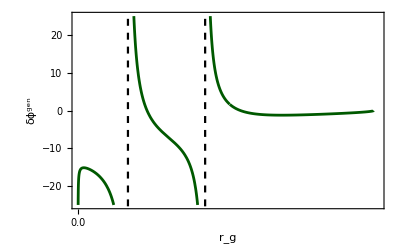

```mathematica
plotδϕgeneric=Show[Plot[corrPlunge["δϕpar"][r],{r,0,r1gPlunge},PlotStyle->{DarkGreen},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δϕ^gen",Black,21]},FrameTicks->{{xlδϕgenericplunge,None},{xbgenericplunge,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,r1gPlunge+0.05},{-25,25}},ImageMargins->10,ImagePadding->{{85, 10}, {Automatic, 10}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aPlunge^2),-120},{1+√(1-aPlunge^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aPlunge^2),-120},{1-√(1-aPlunge^2),120}}]}]]
```

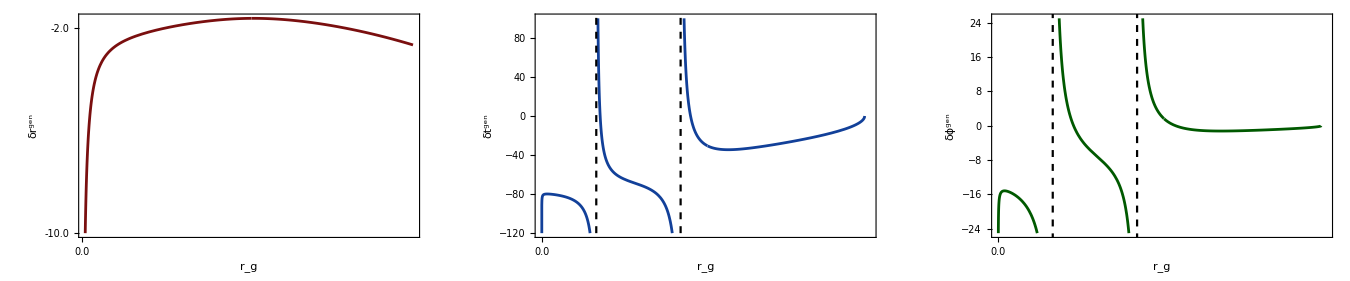

```mathematica
shiftgenericplungeplots=GraphicsRow[{plotδrgeneric,plotδtgeneric,plotδϕgeneric},Spacings->16,ImageSize->1350]
```

```mathematica
(*Export["shift_generic_plunge_plots.pdf",shiftgenericplungeplots]*)
```

shift_generic_plunge_plots.pdf

#### Spin correction plunge related to periodic orbits - equatorial plane

```mathematica
xbPBO=Join[Table[{0.1i,,{0.015,0}},{i,0,100}],Table[{0.5i,Integerise[0.5i],{0.03,0}},{i,0,50}]];
xlδrPBO=Join[Table[{0.25i,,{0.015,0}},{i,-100,0}],Table[{i,Integerise[i],{0.03,0}},{i,-50,0}]];
xlδtPBO=Join[Table[{5i,,{0.015,0}},{i,-100,100}],Table[{25i,Integerise[25i],{0.03,0}},{i,-50,50}]];
xlδϕPBO=Join[Table[{2.5i,,{0.015,0}},{i,-100,100}],Table[{10i,Integerise[10i],{0.03,0}},{i,-50,50}]];
```

```mathematica
aPBO=0.9`55;
eccPBO=0.32`55;
```

```mathematica
pPBO=KerrGeoSeparatrix[aPBO,eccPBO,1]+1;
```

```mathematica
AbsoluteTiming[corrPBO=KerrNearEqSpinOrbitCorrFEPlungeBoundOrbit[aPBO,pPBO,eccPBO,1];]
```

{0.002901,Null}

```mathematica
r3gPBO=2/(1-corrPBO["Eg"]^2)-(pPBO/(1-eccPBO)+pPBO/(1+eccPBO));
```

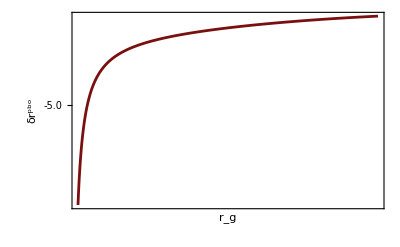

```mathematica
plotδrPBO=Plot[corrPBO["δrpar"][r],{r,0,r3gPBO},PlotStyle->DarkRed,Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δr^pbo",Black,21]},FrameTicks->{{xlδrPBO,None},{xbPBO,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,r3gPBO},{0,-10}},ImageMargins->10,ImagePadding->{{80, 10}, {Automatic, 10}}]
```

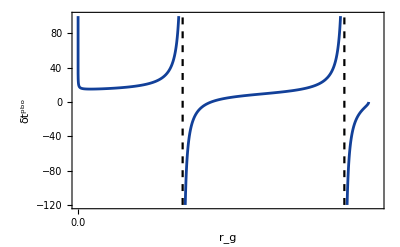

```mathematica
plotδtPBO=Show[Plot[corrPBO["δtpar"][r],{r,0,r3gPBO},PlotStyle->{DarkBlue},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δt^pbo",Black,21]},FrameTicks->{{xlδtPBO,None},{xbPBO,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,r3gPBO+0.05},{-120,100}},ImageMargins->10,ImagePadding->{{85, 10}, {Automatic, 10}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aPBO^2),-120},{1+√(1-aPBO^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aPBO^2),-120},{1-√(1-aPBO^2),120}}]}]]
```

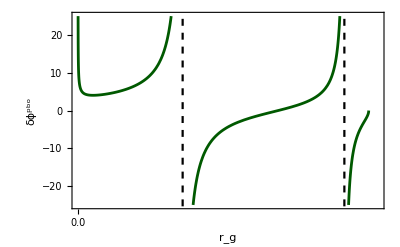

```mathematica
plotδϕPBO=Show[Plot[corrPBO["δϕpar"][r],{r,0,r3gPBO},PlotStyle->{DarkGreen},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δϕ^pbo",Black,21]},FrameTicks->{{xlδϕPBO,None},{xbPBO,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,r3gPBO+0.05},{-25,25}},ImageMargins->10,ImagePadding->{{85, 10}, {Automatic, 10}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aPBO^2),-120},{1+√(1-aPBO^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aPBO^2),-120},{1-√(1-aPBO^2),120}}]}]]
```

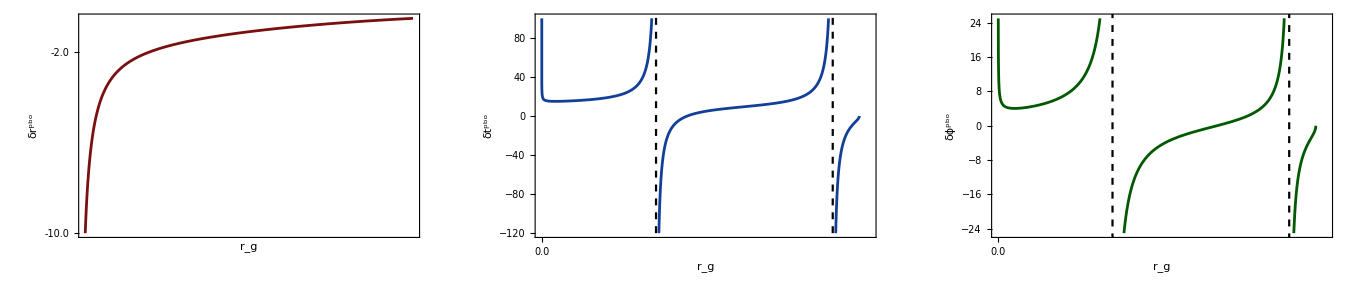

```mathematica
shiftPBOplots=GraphicsRow[{plotδrPBO,plotδtPBO,plotδϕPBO},Spacings->16,ImageSize->1350]
```

```mathematica
(*Export["shift_PBO_plots.pdf",shiftPBOplots]*)
```

#### Spin correction critical plunge+homoclinic motion - equatorial plane

```mathematica
xbCritPlunge=Join[Table[{0.1i,,{0.015,0}},{i,0,100}],Table[{0.5i,Integerise[0.5i],{0.03,0}},{i,0,50}]];
xlδrCritPlunge=Join[Table[{0.25i,,{0.015,0}},{i,-100,0}],Table[{i,Integerise[i],{0.03,0}},{i,-50,0}]];
xlδtCritPlunge=Join[Table[{5i,,{0.015,0}},{i,-100,100}],Table[{25i,Integerise[25i],{0.03,0}},{i,-50,50}]];
xlδϕCritPlunge=Join[Table[{2.5i,,{0.015,0}},{i,-100,100}],Table[{10i,Integerise[10i],{0.03,0}},{i,-50,50}]];
```

```mathematica
aCritPlunge=0.9`55;
eccCritPlunge=0.32`55;
```

```mathematica
pCritPlunge=KerrGeoSeparatrix[aCritPlunge,eccCritPlunge,1];
```

```mathematica
AbsoluteTiming[corrCritPlunge=KerrNearEqSpinOrbitCorrFECritPlunge[aCritPlunge,pCritPlunge,eccCritPlunge,1];]
```

{0.001782,Null}

```mathematica
AbsoluteTiming[corrHom=KerrNearEqSpinOrbitCorrFEHom[aCritPlunge,pCritPlunge,eccCritPlunge,1];]
```

{0.008115,Null}

```mathematica
r1gCritPlunge=pCritPlunge/(1-eccCritPlunge);
r2gCritPlunge=pCritPlunge/(1+eccCritPlunge);
```

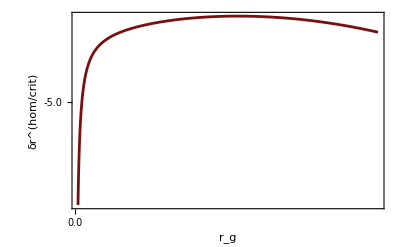

```mathematica
plotδrCritPlunge=Plot[corrCritPlunge["δrpar"][r],{r,0,r1gCritPlunge},PlotStyle->DarkRed,Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δr^(hom/crit)",Black,21]},FrameTicks->{{xlδrCritPlunge,None},{xbCritPlunge,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{0,r1gCritPlunge},{0,-10}},ImageMargins->10,ImagePadding->{{80, 10}, {Automatic, 10}}]
```

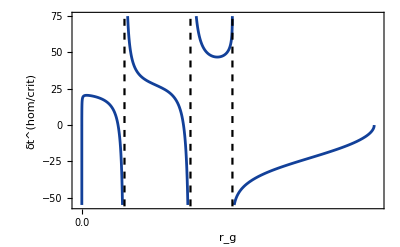

```mathematica
plotδtCritPlunge=Show[
Plot[corrHom["δtpar"][r],{r,r2gCritPlunge,r1gCritPlunge},PlotStyle->{DarkBlue},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δt^(hom/crit)",Black,21]},FrameTicks->{{xlδtCritPlunge,None},{xbCritPlunge,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{-0.05,r1gCritPlunge+0.05},{-55,75}},ImageMargins->10,ImagePadding->{{85, 10}, {Automatic, 10}}],
Plot[corrCritPlunge["δtpar"][r],{r,0,r2gCritPlunge},PlotStyle->{DarkBlue},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δt^(hom/crit)",Black,21]},FrameTicks->{{xlδtCritPlunge,None},{xbCritPlunge,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{-0.05,r1gCritPlunge+0.05},{-55,75}},ImageMargins->10,ImagePadding->{{85, 10}, {Automatic, 10}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{r2gCritPlunge,-120},{r2gCritPlunge,120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aCritPlunge^2),-120},{1+√(1-aCritPlunge^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aCritPlunge^2),-120},{1-√(1-aCritPlunge^2),120}}]}]]
```

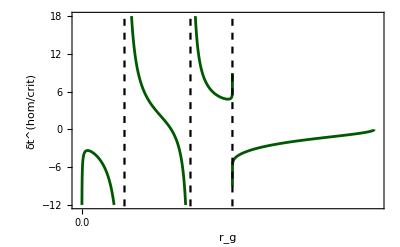

```mathematica
plotδϕCritPlunge=Show[
Plot[corrHom["δϕpar"][r],{r,r2gCritPlunge,r1gCritPlunge},PlotStyle->{DarkGreen},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δt^(hom/crit)",Black,21]},FrameTicks->{{xlδϕCritPlunge,None},{xbPBO,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{-0.05,r1gCritPlunge+0.05},{-12,18}},ImageMargins->10,ImagePadding->{{85, 10}, {Automatic, 10}}],
Plot[corrCritPlunge["δϕpar"][r],{r,0,r2gCritPlunge},PlotStyle->{DarkGreen},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,21],Style["δt^(hom/crit)",Black,21]},FrameTicks->{{xlδϕCritPlunge,None},{xbPBO,None}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotRange->{{-0.05,r1gCritPlunge+0.05},{-12,18}},ImageMargins->10,ImagePadding->{{85, 10}, {Automatic, 10}}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{r2gCritPlunge,-120},{r2gCritPlunge,120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1+√(1-aCritPlunge^2),-120},{1+√(1-aCritPlunge^2),120}}]}],Graphics[{Black,Thickness[0.004],Dashed,Line[{{1-√(1-aCritPlunge^2),-120},{1-√(1-aCritPlunge^2),120}}]}]]
```

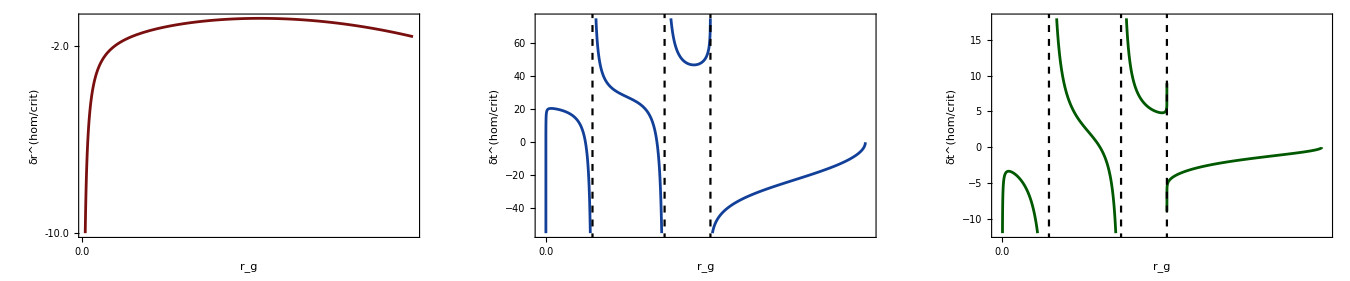

```mathematica
shiftCritPlungeplots=GraphicsRow[{plotδrCritPlunge,plotδtCritPlunge,plotδϕCritPlunge},Spacings->16,ImageSize->1350]
```

```mathematica
(*Export["shift_critical_plunge_plots.pdf",shiftCritPlungeplots]*)
```

shift_critical_plunge_plots.pdf

```mathematica
(*Show[Plot[corrCritPlunge["rg"][λ]+r2gCritPlunge,{λ,-10,0},PlotRange->All],Plot[corrHom["rg"][λ]-r1gCritPlunge+r2gCritPlunge,{λ,0,10},PlotRange->All]]*)
```

## Showcase orbits - fixed eccentricity

For plots

```mathematica
Integerise[num_]:=If[Round[num]==num,ToString[Round@num]<>".0",ToString@num]
```

#### Showcase ISCO plunge

```mathematica
aISCOplunge=0.9`55;
```

```mathematica
pISCOplunge=KerrGeoSeparatrix[aISCOplunge,0,1]
```

2.3208830417618872467900861919226860889786023247688005

```mathematica
rp=1+√(1-aISCOplunge^2);
rm=1-√(1-aISCOplunge^2);
```

```mathematica
AbsoluteTiming[corrISCOplunge=KerrNearEqSpinOrbitCorrFEISCOPlunge[aISCOplunge,1];]
```

{0.000611,Null}

```mathematica
xiscoplungeshowcase=Join[Table[{0.1i,,{0.015,0}},{i,-100,100}],Table[{1i,Integerise[1i],{0.03,0}},{i,-50,50}]];
yiscoplungeshowcase=Join[Table[{0.1i,,{0.015,0}},{i,-100,100}],Table[{0.5i,Integerise[0.5i],{0.03,0}},{i,-50,50}]];
ziscoplungeshowcase=Join[Table[{0.01i,,{0.015,0}},{i,-100,100}],Table[{0.05i,Integerise[0.05i],{0.03,0}},{i,-50,50}]];
```

```mathematica
δrparISCOPlunge[r_]:=corrISCOplunge["δrpar"][r];
```

```mathematica
ϕgISCOPlunge[r_]:=corrISCOplunge["ϕrg"][r];
δϕparISCOPlunge[r_]:=corrISCOplunge["δϕpar"][r];
```

```mathematica
δzortISCOPlunge[r_]:=corrISCOplunge["δzort"][r];
```

```mathematica
χpar=1/2;
q=1/20;
```

```mathematica
σpar=q*χpar;
σort=q*√(1-χpar^2);
```

```mathematica
xgISCOplungefun[r_]:=r Cos[ϕgISCOPlunge[r]];
ygISCOplungefun[r_]:=r Sin[ϕgISCOPlunge[r]];
```

```mathematica
xspinISCOplungefun[r_]:=(r+σpar δrparISCOPlunge[r])Cos[ϕgISCOPlunge[r]+σpar δϕparISCOPlunge[r]];
yspinISCOplungefun[r_]:=(r+σpar δrparISCOPlunge[r]) Sin[ϕgISCOPlunge[r]+σpar δϕparISCOPlunge[r]];
```

```mathematica
BirdsEyeISCOPlungeGeopt1=ParametricPlot[{xgISCOplungefun[r],ygISCOplungefun[r]},{r,rp+1/20000,pISCOplunge-1/100},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xiscoplungeshowcase,True},{xiscoplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->6];
```

```mathematica
BirdsEyeISCOPlungeGeopt2=ParametricPlot[{xgISCOplungefun[r],ygISCOplungefun[r]},{r,rm+1/20000,rp-1/20000},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xiscoplungeshowcase,True},{xiscoplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->6];
```

```mathematica
BirdsEyeISCOPlungeGeopt3=ParametricPlot[{xgISCOplungefun[r],ygISCOplungefun[r]},{r,0+1/1000,rm-1/20000},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xiscoplungeshowcase,True},{xiscoplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->6];
```

```mathematica
BirdsEyeISCOPlungeSpinpt1=ParametricPlot[{xspinISCOplungefun[r],yspinISCOplungefun[r]},{r,rp+1/1000,pISCOplunge-1/100},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xiscoplungeshowcase,True},{xiscoplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->10];
```

```mathematica
BirdsEyeISCOPlungeSpinpt2=ParametricPlot[{xspinISCOplungefun[r],yspinISCOplungefun[r]},{r,rm+1/1000,rp-1/1000},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xiscoplungeshowcase,True},{xiscoplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->10];
```

```mathematica
BirdsEyeISCOPlungeSpinpt3=ParametricPlot[{xspinISCOplungefun[r],yspinISCOplungefun[r]},{r,0+1/5,rm-1/1000},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xiscoplungeshowcase,True},{xiscoplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->10];
```

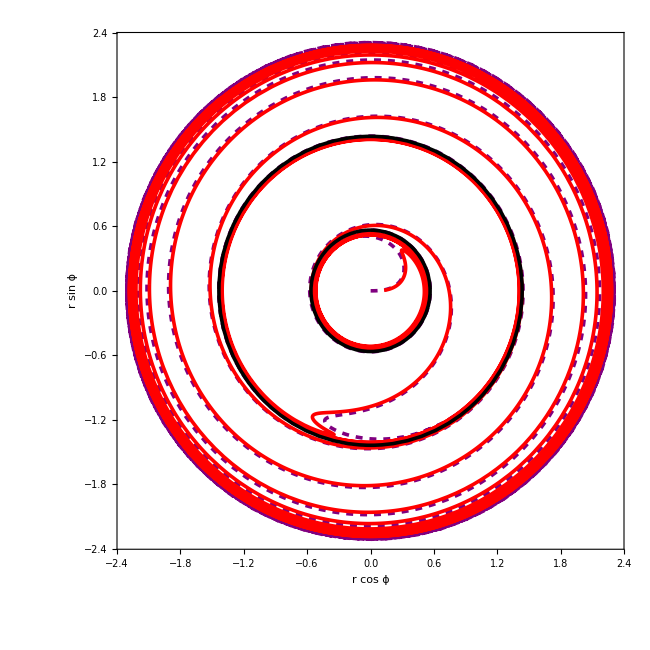

```mathematica
BirdsEyeISCOPlunge=Show[BirdsEyeISCOPlungeGeopt1,BirdsEyeISCOPlungeGeopt2,BirdsEyeISCOPlungeGeopt3,BirdsEyeISCOPlungeSpinpt1,BirdsEyeISCOPlungeSpinpt2,BirdsEyeISCOPlungeSpinpt3,Graphics[{Black,Thickness[0.004],Circle[{0,0},1+√(1-aISCOplunge^2)]}],Graphics[{Black,Thickness[0.004],Circle[{0,0},1-√(1-aISCOplunge^2)]}],ImageSize->650]
```

```mathematica
(*Export["isco_plunge_birds_eye.pdf",BirdsEyeISCOPlunge]*)
```

isco_plunge_birds_eye.pdf

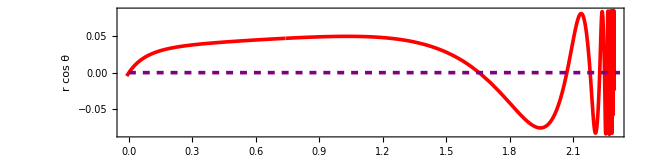

```mathematica
MeridionalISCOPlunge=Show[ParametricPlot[{(r+σpar δrparISCOPlunge[r]) Sin[π/2-σort δzortISCOPlunge[r]],(r+σpar δrparISCOPlunge[r])Cos[π/2-σort δzortISCOPlunge[r]]},{r,1/10,pISCOplunge},Method->{"ShrinkWrap"->True},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r sin θ",18],Style["r cos θ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},AspectRatio->1/4,FrameTicks->{{ziscoplungeshowcase,True},{yiscoplungeshowcase,True}}],Graphics[{Purple,Thickness[0.004],Dashed,Line[{{0,0},{pISCOplunge,0}}]}],ImageSize->650]
```

```mathematica
(*Export["isco_plunge_meridional.pdf",MeridionalISCOPlunge]*)
```

isco_plunge_meridional.pdf

#### Showcase homoclinic orbits

```mathematica
aCritPlunge=0.9`55;
eccCritPlunge=0.32`55;
```

```mathematica
pCritPlunge=KerrGeoSeparatrix[aCritPlunge,eccCritPlunge,1];
```

```mathematica
AbsoluteTiming[corrCritPlunge=KerrNearEqSpinOrbitCorrFECritPlunge[aCritPlunge,pCritPlunge,eccCritPlunge,1];]
```

{0.002841,Null}

```mathematica
AbsoluteTiming[corrHom=KerrNearEqSpinOrbitCorrFEHom[aCritPlunge,pCritPlunge,eccCritPlunge,1];]
```

{0.012901,Null}

```mathematica
r1gCritPlunge=pCritPlunge/(1-eccCritPlunge);
r2gCritPlunge=pCritPlunge/(1+eccCritPlunge);
```

```mathematica
rp=1+√(1-aCritPlunge^2);
rm=1-√(1-aCritPlunge^2);
```

```mathematica
xcritplungeshowcase=Join[Table[{0.1i,,{0.015,0}},{i,-100,100}],Table[{1i,Integerise[1i],{0.03,0}},{i,-50,50}]];
ycritplungeshowcase=Join[Table[{0.1i,,{0.015,0}},{i,-100,100}],Table[{0.5i,Integerise[0.5i],{0.03,0}},{i,-50,50}]];
zcritplungeshowcase=Join[Table[{0.01i,,{0.015,0}},{i,-100,100}],Table[{0.05i,Integerise[0.05i],{0.03,0}},{i,-50,50}]];
```

```mathematica
δrparCritPlunge[r_]:=corrCritPlunge["δrpar"][r];
δrparHom[r_]:=corrHom["δrpar"][r];
```

```mathematica
ϕgCritPlunge[r_]:=corrCritPlunge["ϕrg"][r];
δϕparCritPlunge[r_]:=corrCritPlunge["δϕpar"][r];
ϕgHom[r_]:=corrHom["ϕrg"][r];
δϕparHom[r_]:=corrHom["δϕpar"][r];
```

```mathematica
δzortCritPlunge[r_]:=corrCritPlunge["δzort"][r];
δzortHom[r_]:=corrHom["δzort"][r];
```

```mathematica
χpar=1/2;
q=1/20;
```

```mathematica
σpar=q*χpar;
σort=q*√(1-χpar^2);
```

```mathematica
xgCritPlungefun[r_]:=r Cos[ϕgCritPlunge[r]];
ygCritPlungefun[r_]:=r Sin[ϕgCritPlunge[r]];
xgHomfun[r_]:=r Cos[ϕgHom[r]];
ygHomfun[r_]:=r Sin[ϕgHom[r]];
```

```mathematica
xspinCritPlungefun[r_]:=(r+σpar δrparCritPlunge[r])Cos[ϕgCritPlunge[r]+σpar δϕparCritPlunge[r]];
yspinCritPlungefun[r_]:=(r+σpar δrparCritPlunge[r]) Sin[ϕgCritPlunge[r]+σpar δϕparCritPlunge[r]];
xspinHomfun[r_]:=(r+σpar δrparHom[r])Cos[ϕgHom[r]+σpar δϕparHom[r]];
yspinHomfun[r_]:=(r+σpar δrparHom[r]) Sin[ϕgHom[r]+σpar δϕparHom[r]];
```

```mathematica
BirdsEyeCritPlungeGeopt1=ParametricPlot[{xgHomfun[r],ygHomfun[r]},{r,r2gCritPlunge+1/20000,r1gCritPlunge},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xcritplungeshowcase,True},{xcritplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->10];
```

```mathematica
BirdsEyeCritPlungeGeopt2=ParametricPlot[{xgCritPlungefun[r],ygCritPlungefun[r]},{r,rp+1/20000,r2gCritPlunge-1/20000},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xcritplungeshowcase,True},{xcritplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->8];
```

```mathematica
BirdsEyeCritPlungeGeopt3=ParametricPlot[{xgCritPlungefun[r],ygCritPlungefun[r]},{r,rm+1/20000,rp-1/20000},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xcritplungeshowcase,True},{xcritplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->8];
```

```mathematica
BirdsEyeCritPlungeGeopt4=ParametricPlot[{xgCritPlungefun[r],ygCritPlungefun[r]},{r,0+1/1000,rm-1/20000},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xcritplungeshowcase,True},{xcritplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->8];
```

```mathematica
BirdsEyeCritPlungeSpinpt1=ParametricPlot[{xspinHomfun[r],yspinHomfun[r]},{r,r2gCritPlunge+1/20000,r1gCritPlunge-10^(-5)},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xcritplungeshowcase,True},{xcritplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->12];
```

```mathematica
BirdsEyeCritPlungeSpinpt2=ParametricPlot[{xspinCritPlungefun[r],yspinCritPlungefun[r]},{r,rp+1/1000,r2gCritPlunge-1/20000},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xcritplungeshowcase,True},{xcritplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->12];
```

```mathematica
BirdsEyeCritPlungeSpinpt3=ParametricPlot[{xspinCritPlungefun[r],yspinCritPlungefun[r]},{r,rm+1/1000,rp-1/1000},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xcritplungeshowcase,True},{xcritplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->12];
```

```mathematica
BirdsEyeCritPlungeSpinpt4=ParametricPlot[{xspinCritPlungefun[r],yspinCritPlungefun[r]},{r,1/10,rm-1/1000},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xcritplungeshowcase,True},{xcritplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->12];
```

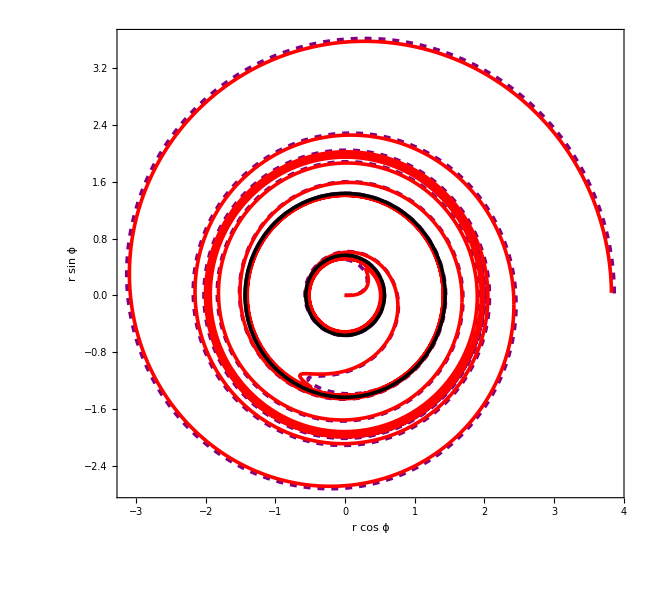

```mathematica
BirdsEyeCritPlunge=Show[BirdsEyeCritPlungeGeopt1,BirdsEyeCritPlungeGeopt2,BirdsEyeCritPlungeGeopt3,BirdsEyeCritPlungeGeopt4,BirdsEyeCritPlungeSpinpt1,BirdsEyeCritPlungeSpinpt2,BirdsEyeCritPlungeSpinpt3,BirdsEyeCritPlungeSpinpt4,Graphics[{Black,Thickness[0.004],Circle[{0,0},1+√(1-aCritPlunge^2)]}],Graphics[{Black,Thickness[0.004],Circle[{0,0},1-√(1-aCritPlunge^2)]}],ImageSize->650]
```

```mathematica
(*Export["crit_plunge_birds_eye.pdf",BirdsEyeCritPlunge]*)
```

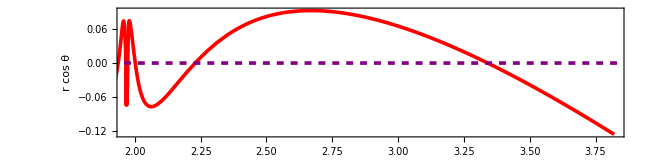

```mathematica
MeridionalCritPlunge=Show[ParametricPlot[{(r+σpar δrparHom[r]) Sin[π/2-σort δzortHom[r]],(r+σpar δrparHom[r])Cos[π/2-σort δzortHom[r]]},{r,r2gCritPlunge,r1gCritPlunge},Method->{"ShrinkWrap"->True},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r sin θ",18],Style["r cos θ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},AspectRatio->1/4,FrameTicks->{{zcritplungeshowcase,True},{ycritplungeshowcase,True}}],ParametricPlot[{(r+σpar δrparCritPlunge[r]) Sin[π/2-σort δzortCritPlunge[r]],(r+σpar δrparCritPlunge[r])Cos[π/2-σort δzortCritPlunge[r]]},{r,1/1000,r2gCritPlunge},Method->{"ShrinkWrap"->True},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r sin θ",18],Style["r cos θ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},AspectRatio->1/4,FrameTicks->{{zcritplungeshowcase,True},{ycritplungeshowcase,True}}],Graphics[{Purple,Thickness[0.004],Dashed,Line[{{0,0},{r1gCritPlunge,0}}]}],ImageSize->650]
```

```mathematica
(*Export["crit_plunge_meridional.pdf",MeridionalCritPlunge]*)
```

#### Showcase Generic plunge

```mathematica
aPlunge=0.9`55;
eccPlunge=0.32`55;
```

```mathematica
pPlunge=2.27`55;
```

```mathematica
r1gPlunge=pPlunge/(1-eccPlunge);
```

```mathematica
AbsoluteTiming[corrPlunge=KerrNearEqSpinOrbitCorrFEPlunge[aPlunge,pPlunge,eccPlunge,1];]
```

{0.001758,Null}

```mathematica
rp=1+√(1-aPlunge^2);
rm=1-√(1-aPlunge^2);
```

```mathematica
xplungeshowcase=Join[Table[{0.1i,,{0.015,0}},{i,-100,100}],Table[{1i,Integerise[1i],{0.03,0}},{i,-50,50}]];
yplungeshowcase=Join[Table[{0.1i,,{0.015,0}},{i,-100,100}],Table[{0.5i,Integerise[0.5i],{0.03,0}},{i,-50,50}]];
zplungeshowcase=Join[Table[{0.01i,,{0.015,0}},{i,-100,100}],Table[{0.05i,Integerise[0.05i],{0.03,0}},{i,-50,50}]];
```

```mathematica
δrparPlunge[r_]:=corrPlunge["δrpar"][r];
```

```mathematica
ϕgPlunge[r_]:=corrPlunge["ϕrg"][r];
δϕparPlunge[r_]:=corrPlunge["δϕpar"][r];
```

```mathematica
δzortPlunge[r_]:=corrPlunge["δzort"][r];
```

```mathematica
χpar=1/2;
q=1/20;
```

```mathematica
σpar=q*χpar;
σort=q*√(1-χpar^2);
```

```mathematica
xgPlungefun[r_]:=r Cos[ϕgPlunge[r]];
ygPlungefun[r_]:=r Sin[ϕgPlunge[r]];
```

```mathematica
xspinPlungefun[r_]:=(r+σpar δrparPlunge[r])Cos[ϕgPlunge[r]+σpar δϕparPlunge[r]];
yspinPlungefun[r_]:=(r+σpar δrparPlunge[r]) Sin[ϕgPlunge[r]+σpar δϕparPlunge[r]];
```

```mathematica
BirdsEyePlungeGeopt1=ParametricPlot[{xgPlungefun[r],ygPlungefun[r]},{r,rp+1/20000,r1gPlunge},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xplungeshowcase,True},{xplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->8];
```

```mathematica
BirdsEyePlungeGeopt2=ParametricPlot[{xgPlungefun[r],ygPlungefun[r]},{r,rm+1/20000,rp-1/20000},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xplungeshowcase,True},{xplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->8];
```

```mathematica
BirdsEyePlungeGeopt3=ParametricPlot[{xgPlungefun[r],ygPlungefun[r]},{r,0+1/1000,rm-1/20000},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xplungeshowcase,True},{xplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->8];
```

```mathematica
BirdsEyePlungeSpinpt1=ParametricPlot[{xspinPlungefun[r],yspinPlungefun[r]},{r,rp+1/1000,r1gPlunge-10^(-5)},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xplungeshowcase,True},{xplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->12];
```

```mathematica
BirdsEyePlungeSpinpt2=ParametricPlot[{xspinPlungefun[r],yspinPlungefun[r]},{r,rm+1/1000,rp-1/1000},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xplungeshowcase,True},{xplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->12];
```

```mathematica
BirdsEyePlungeSpinpt3=ParametricPlot[{xspinPlungefun[r],yspinPlungefun[r]},{r,0+1/5,rm-1/1000},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xplungeshowcase,True},{xplungeshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->12];
```

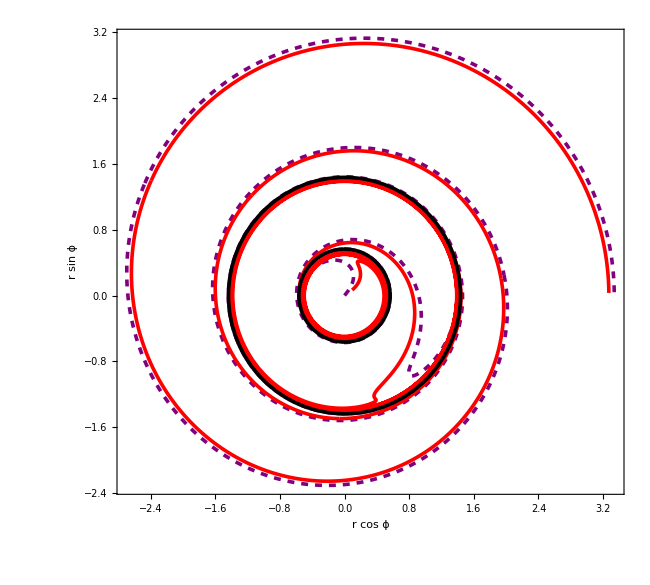

```mathematica
BirdsEyePlunge=Show[BirdsEyePlungeGeopt1,BirdsEyePlungeGeopt2,BirdsEyePlungeGeopt3,BirdsEyePlungeSpinpt1,BirdsEyePlungeSpinpt2,BirdsEyePlungeSpinpt3,Graphics[{Black,Thickness[0.004],Circle[{0,0},1+√(1-aPlunge^2)]}],Graphics[{Black,Thickness[0.004],Circle[{0,0},1-√(1-aPlunge^2)]}],ImageSize->650]
```

```mathematica
(*Export["plunge_birds_eye.pdf",BirdsEyePlunge]*)
```

plunge_birds_eye.pdf

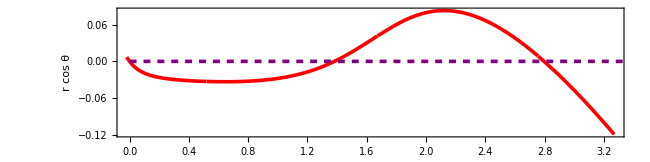

```mathematica
MeridionalPlunge=Show[ParametricPlot[{(r+σpar δrparPlunge[r]) Sin[π/2-σort δzortPlunge[r]],(r+σpar δrparPlunge[r])Cos[π/2-σort δzortPlunge[r]]},{r,1/10,r1gPlunge},Method->{"ShrinkWrap"->True},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r sin θ",18],Style["r cos θ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},AspectRatio->1/4,FrameTicks->{{zplungeshowcase,True},{yplungeshowcase,True}}],Graphics[{Purple,Thickness[0.004],Dashed,Line[{{0,0},{r1gPlunge,0}}]}],ImageSize->650]
```

```mathematica
(*Export["plunge_meridional.pdf",MeridionalPlunge]*)
```

plunge_meridional.pdf

#### Showcase Plunge related to periodic Orbits

```mathematica
aPBO=0.9`55;
eccPBO=0.32`55;
```

```mathematica
pPBO=KerrGeoSeparatrix[aPBO,eccPBO,1]+1
```

3.6270469505690145892193952028064598761326729466885252

```mathematica
AbsoluteTiming[corrPBO=KerrNearEqSpinOrbitCorrFEPlungeBoundOrbit[aPBO,pPBO,eccPBO,1];]
```

{0.022635,Null}

```mathematica
r3gPBO=2/(1-corrPBO["Eg"]^2)-(pPBO/(1-eccPBO)+pPBO/(1+eccPBO));
```

```mathematica
rp=1+√(1-aPBO^2);
rm=1-√(1-aPBO^2);
```

```mathematica
xpboshowcase=Join[Table[{0.1i,,{0.015,0}},{i,-100,100}],Table[{1i,Integerise[1i],{0.03,0}},{i,-50,50}]];
ypboshowcase=Join[Table[{0.1i,,{0.015,0}},{i,-100,100}],Table[{0.5i,Integerise[0.5i],{0.03,0}},{i,-50,50}]];
zpboshowcase=Join[Table[{0.01i,,{0.015,0}},{i,-100,100}],Table[{0.05i,Integerise[0.05i],{0.03,0}},{i,-50,50}]];
```

```mathematica
δrparPBO[r_]:=corrPBO["δrpar"][r];
```

```mathematica
ϕgPBO[r_]:=corrPBO["ϕrg"][r];
δϕparPBO[r_]:=corrPBO["δϕpar"][r];
```

```mathematica
δzortPBO[r_]:=corrPBO["δzort"][r];
```

```mathematica
χpar=1/2;
q=1/20;
```

```mathematica
σpar=q*χpar;
σort=q*√(1-χpar^2);
```

```mathematica
xgPBOfun[r_]:=r Cos[ϕgPBO[r]];
ygPBOfun[r_]:=r Sin[ϕgPBO[r]];
```

```mathematica
xspinPBOfun[r_]:=(r+σpar δrparPBO[r])Cos[ϕgPBO[r]+σpar δϕparPBO[r]];
yspinPBOfun[r_]:=(r+σpar δrparPBO[r]) Sin[ϕgPBO[r]+σpar δϕparPBO[r]];
```

```mathematica
BirdsEyePBOGeopt1=ParametricPlot[{xgPBOfun[r],ygPBOfun[r]},{r,rp+1/20000,r3gPBO},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xpboshowcase,True},{xpboshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->6];
```

```mathematica
BirdsEyePBOGeopt2=ParametricPlot[{xgPBOfun[r],ygPBOfun[r]},{r,rm+1/20000,rp-1/20000},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xpboshowcase,True},{xpboshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->6];
```

```mathematica
BirdsEyePBOGeopt3=ParametricPlot[{xgPBOfun[r],ygPBOfun[r]},{r,0+1/1000,rm-1/20000},PlotStyle->{Purple,Thickness[0.004],Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xpboshowcase,True},{xpboshowcase,True}},WorkingPrecision->20,PlotPoints->{500,500},MaxRecursion->6];
```

```mathematica
BirdsEyePBOSpinpt1=ParametricPlot[{xspinPBOfun[r],yspinPBOfun[r]},{r,rp+1/1000,r3gPBO-10^(-6)},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xpboshowcase,True},{xpboshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->10];
```

```mathematica
BirdsEyePBOSpinpt2=ParametricPlot[{xspinPBOfun[r],yspinPBOfun[r]},{r,rm+1/1000,rp-1/1000},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xpboshowcase,True},{xpboshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->10];
```

```mathematica
BirdsEyePBOSpinpt3=ParametricPlot[{xspinPBOfun[r],yspinPBOfun[r]},{r,0+1/5,rm-1/1000},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r cos ϕ",18],Style["r sin ϕ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Method->{"ShrinkWrap"->True},FrameTicks->{{xpboshowcase,True},{xpboshowcase,True}},WorkingPrecision->20,PlotPoints->{750,750},MaxRecursion->10];
```

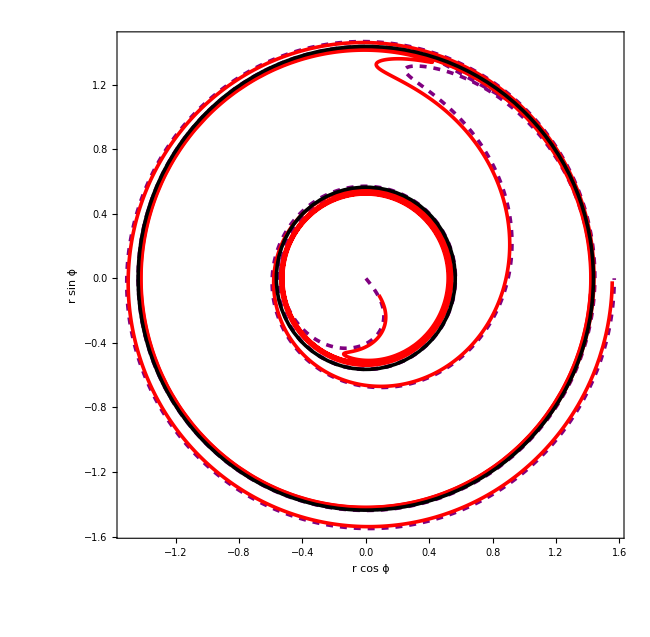

```mathematica
BirdsEyePBO=Show[BirdsEyePBOGeopt1,BirdsEyePBOGeopt2,BirdsEyePBOGeopt3,BirdsEyePBOSpinpt1,BirdsEyePBOSpinpt2,BirdsEyePBOSpinpt3,Graphics[{Black,Thickness[0.004],Circle[{0,0},1+√(1-aPBO^2)]}],Graphics[{Black,Thickness[0.004],Circle[{0,0},1-√(1-aPBO^2)]}],ImageSize->650]
```

```mathematica
(*Export["PBO_birds_eye.pdf",BirdsEyePBO]*)
```

```mathematica
"PBO_birds_eye.pdf"
```

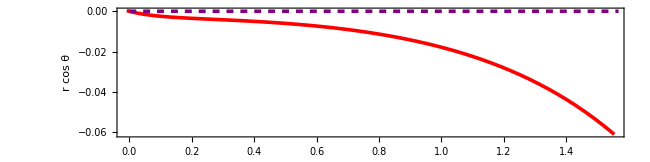

```mathematica
MeridionalPBO=Show[ParametricPlot[{(r+σpar δrparPBO[r]) Sin[π/2-σort δzortPBO[r]],(r+σpar δrparPBO[r])Cos[π/2-σort δzortPBO[r]]},{r,1/10,r3gPBO},Method->{"ShrinkWrap"->True},PlotStyle->{Red,Thickness[0.004]},Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["r sin θ",18],Style["r cos θ",18],"",""},LabelStyle->{FontSize->16,FontFamily->"Times",Black},AspectRatio->1/4,FrameTicks->{{zpboshowcase,True},{ypboshowcase,True}}],Graphics[{Purple,Thickness[0.004],Dashed,Line[{{0,0},{r3gPBO,0}}]}],ImageSize->650]
```

```mathematica
(*Export["PBO_meridional.pdf",MeridionalPBO]*)
```